### Plots for Figure 1

#### Figure 1 (b)

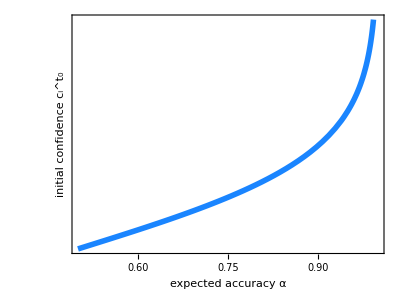

/Users/joefresna/Google Drive/DiODe/Manuscripts/DDM-on-Net/graphics/conf_sdt.pdf

```mathematica
axesThickness=0.003;
lineThickness=0.01;
labelSize=25;
tickSize=20;
(* Colour-blind-friendly colours *)colours={RGBColor["#1A85FF"],RGBColor["#D41159"]}; 
Plot[Log[x/(1-x)],{x,0.5,1},
FrameLabel->{Style["expected accuracy α",Black,LineSpacing->{0,20}],Style["initial confidence c_i^t_0",Black]},
PlotStyle->Directive[{colours[[1]],Thickness[lineThickness]}],
FrameTicks->{True,False},
FrameTicksStyle->tickSize,
Frame->{True,True,True,True},
FrameTicks->False,
AspectRatio->3/4,LabelStyle->{labelSize,Bold},
FrameStyle->Directive[{Gray,Thickness[axesThickness]}],
ImageSize->400]
Export["/Users/joefresna/Google Drive/DiODe/Manuscripts/DDM-on-Net/graphics/conf_sdt.pdf",%]
```

#### Figure 1 (d)

```mathematica
timestepsize=0.001;
maxtime=10;
drift=0.1;
noise=0.5;
thresh=1;
SeedRandom[25631113];
fpt1=Table[{dataTmp=RandomFunction[WienerProcess[driftV,noise],{0,maxtime,timestepsize}],restmp={Position[dataTmp[[2,1,1]],SelectFirst[dataTmp[[2,1,1]],#>thresh&]],Position[dataTmp[[2,1,1]],SelectFirst[dataTmp[[2,1,1]],#<-thresh&]]},Range[0,maxtime,timestepsize][[Min[restmp]]]},{driftV,{-0.1,-0.05,0,0.05,0.1,0.15,0.2,0.25,0.3}}];
```

```mathematica
trimmed=Table[fpt1[[v,1]]["Path",All][[1,;;Min[fpt1[[v,2]]]]],{v,1,Length[fpt1]}];
topThresh=Select[fpt1,Position[#[[2]],Min[#[[2]]]][[1,1]]==1&][[All,3]];
bottomThresh=Select[fpt1,Position[#[[2]],Min[#[[2]]]][[1,1]]==2&][[All,3]];
topThreshLine=Join[
Transpose[{Join[Transpose[{topThresh}],ConstantArray[{thresh},Length[topThresh]],2]}],Transpose[{Join[Transpose[{topThresh}],ConstantArray[{-thresh},Length[topThresh]],2]}],2];
topThreshDot=Transpose[{Join[Transpose[{topThresh}],ConstantArray[{thresh},Length[topThresh]],2]}];
bottomThreshDot=Transpose[{Join[Transpose[{bottomThresh}],ConstantArray[{-thresh},Length[bottomThresh]],2]}];
```

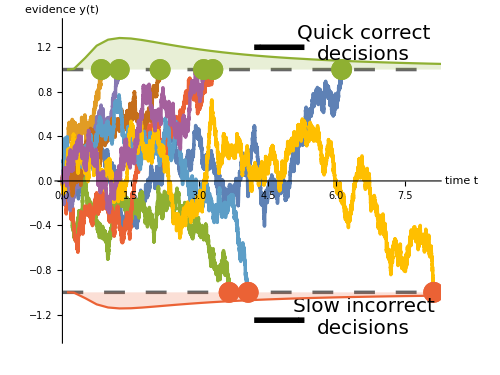

```mathematica
saveImg=True;
fptDataPlus=Import["/Users/joefresna/Google Drive/DiODe/Manuscripts/DDM-on-Net/analyses/data/data_plus.txt","Table"];
fptDataMinus=Import["/Users/joefresna/Google Drive/DiODe/Manuscripts/DDM-on-Net/analyses/data/data_minus.txt","Table"];
axesThickness=0.005;
threshLineThickness=0.005;
pointSize=0.03;
Show[
ListLinePlot[trimmed,LabelStyle->{labelSize,Bold},TicksStyle->tickSize,AxesLabel->{Style["time t",Black],Style["evidence y(t)",Black]},Ticks->{False,True},PlotStyle->Thickness[threshLineThickness],AspectRatio->3/4,AxesStyle->{{Arrowheads[{0.0,0.05}],Gray,Thickness[axesThickness]},{Gray,Thickness[axesThickness]}},
ImageSize->500,PlotRange->{Automatic,{-thresh*1.4,thresh*1.4}}
],
Graphics[{Directive[{Thickness[threshLineThickness],Dashing[0.03],GrayLevel[0.4]}],Line[{{{0,thresh},{Max[trimmed],thresh}},{{0,-thresh},{Max[trimmed],-thresh}}}]}],
(*Graphics[{Directive[{Thickness[lineThickness/1.5],colours[[3]]}],Line[topThreshLine]}]*)
ListPlot[topThreshDot,PlotStyle->Directive[{colours[[3]],PointSize[pointSize]}]],
ListPlot[bottomThreshDot,PlotStyle->Directive[{colours[[4]],PointSize[pointSize]}]],
ListLinePlot[(fptDataPlus/.{x_,y_}->{x,3y})+Table[{0,1},Length[fptDataPlus]],PlotStyle->Directive[{colours[[3]]}],Filling->thresh],
ListLinePlot[(fptDataMinus/.{x_,y_}->{x,3y})+Table[{0,1},Length[fptDataMinus]],ScalingFunctions->{Identity,"Reverse"},PlotStyle->Directive[{colours[[4]]}],Filling->thresh],
Graphics[{
Text[Style["Quick correct\ndecisions",{20,LineSpacing->{0,15}}],{6.6,thresh*1.23}],
{Directive[{Black,Thickness[lineThickness]}],Arrow[{{5.3,thresh*1.2},{4.2,thresh*1.2}}]},
Text[Style["Slow incorrect\ndecisions",{20,LineSpacing->{0,15}}],{6.6,-thresh*1.23}],
{Directive[{Black,Thickness[lineThickness]}],Arrow[{{4.2,-thresh*1.25},{5.3,-thresh*1.25}}]}
}]
]
If[saveImg,Export["/Users/joefresna/Google Drive/DiODe/Manuscripts/DDM-on-Net/graphics/DDMs.pdf",%]];
```

#### Figure 1 (e)

```mathematica
(*
costMatrix=[1,100]
noiseStdDev=1
prior=0.5;
meanDrift=0.2;
first item is std-dev
*)confData={{0.5,0.25000000000000000000,0.2892708710721782},{0.5,0.50000000000000000000,0.27949871664825987},{0.5,0.75000000000000000000,0.27060436347443717},{0.5,1.00000000000000000000,0.26246638299462},{0.5,1.25000000000000000000,0.25498537707273633},{0.5,1.50000000000000000000,0.24807912796134732},{0.5,1.75000000000000000000,0.24167898607031754},{0.5,2.00000000000000000000,0.23572714009950643},{0.5,2.25000000000000000000,0.2301745265537082},{0.5,2.50000000000000000000,0.22497920951171402},{0.5,2.75000000000000000000,0.2201051109814921},{0.5,3.00000000000000000000,0.21552100589186188},{0.5,3.25000000000000000000,0.21119971913526708},{0.5,3.50000000000000000000,0.20711747850962278},{0.5,3.75000000000000000000,0.20325338912597268},{0.5,4.00000000000000000000,0.19958900331305687},{0.5,4.25000000000000000000,0.1961079662351009},{0.5,4.50000000000000000000,0.19279572201065936},{0.5,4.75000000000000000000,0.18963926853187824},{0.5,5.00000000000000000000,0.1866269517555701},{0.5,5.25000000000000000000,0.18374829219312985},{0.5,5.50000000000000000000,0.18099383782618814},{0.5,5.75000000000000000000,0.1783550388342839},{0.5,6.00000000000000000000,0.1758241403723462},{0.5,6.25000000000000000000,0.17339409070765116},{0.5,6.50000000000000000000,0.17105846148601622},{0.5,6.75000000000000000000,0.16881137917644495},{0.5,7.00000000000000000000,0.1666474652713179},{0.5,7.25000000000000000000,0.1645617841871957},{0.5,7.50000000000000000000,0.16254979768906888},{0.5,7.75000000000000000000,0.16060732509957193},{0.5,8.00000000000000000000,0.1587305072474457},{0.5,8.25000000000000000000,0.15691577673569282},{0.5,8.50000000000000000000,0.15515982952600843},{0.5,8.75000000000000000000,0.1534596007718357},{0.5,9.00000000000000000000,0.1518122431150914},{0.5,9.25000000000000000000,0.15021510733387855},{0.5,9.50000000000000000000,0.1486657250467886},{0.5,9.75000000000000000000,0.14716179322104325},{0.5,10.00000000000000000000,0.14570116026683613},{0.5,10.25000000000000000000,0.1442818135299196},{0.5,10.50000000000000000000,0.14290186801967927},{0.5,10.75000000000000000000,0.14155955623136685},{0.5,11.00000000000000000000,0.14025321893946804},{0.5,11.25000000000000000000,0.13898129685483343},{0.5,11.50000000000000000000,0.13774232305165182},{0.5,11.75000000000000000000,0.13653491608190713},{0.5,12.00000000000000000000,0.13535777370494453},{0.5,12.25000000000000000000,0.13420966716840702},{0.5,12.50000000000000000000,0.1330894359842867},{0.5,12.75000000000000000000,0.13199598315034658},{0.5,13.00000000000000000000,0.13092827077283178},{0.5,13.25000000000000000000,0.1298890119426926},{0.5,13.50000000000000000000,0.1288701899776754},{0.5,13.75000000000000000000,0.12787425695350077},{0.5,14.00000000000000000000,0.1269003733256298},{0.5,14.25000000000000000000,0.12594774230232836},{0.5,14.50000000000000000000,0.12501560712519774},{0.5,14.75000000000000000000,0.12410324854971323},{0.5,15.00000000000000000000,0.12320998250911991},{0.5,15.25000000000000000000,0.12233515794664572},{0.5,15.50000000000000000000,0.12147815480241779},{0.5,15.75000000000000000000,0.12063838214273111},{0.5,16.00000000000000000000,0.1198152764204485},{0.5,16.25000000000000000000,0.11900829985630683},{0.5,16.50000000000000000000,0.11821693893181134},{0.5,16.75000000000000000000,0.1174407029851975},{0.5,17.00000000000000000000,0.11667912290267002},{0.5,17.25000000000000000000,0.11593174989777517},{0.5,17.50000000000000000000,0.11519815437235827},{0.5,17.75000000000000000000,0.11447792485308668},{0.5,18.00000000000000000000,0.11377066699800509},{0.5,18.25000000000000000000,0.11306446352924068},{0.5,18.50000000000000000000,0.1123822985765921},{0.5,18.75000000000000000000,0.11171211021100928},{0.5,19.00000000000000000000,0.11105355724204585},{0.5,19.25000000000000000000,0.11040631117501629},{0.5,19.50000000000000000000,0.10977005563487645},{0.5,19.75000000000000000000,0.10914448582506149},{0.75,0.25000000000000000000,0.42484154218834685},{0.75,0.50000000000000000000,0.39725124599266176},{0.75,0.75000000000000000000,0.3742641406514035},{0.75,1.00000000000000000000,0.3547423192597657},{0.75,1.25000000000000000000,0.3379039157336266},{0.75,1.50000000000000000000,0.32319216298314896},{0.75,1.75000000000000000000,0.3101987106193391},{0.75,2.00000000000000000000,0.29861654195606174},{0.75,2.25000000000000000000,0.2882098984333473},{0.75,2.50000000000000000000,0.27879441192252985},{0.75,2.75000000000000000000,0.27022359583668465},{0.75,3.00000000000000000000,0.2623794264472933},{0.75,3.25000000000000000000,0.25516562978905855},{0.75,3.50000000000000000000,0.24850280284996268},{0.75,3.75000000000000000000,0.2423248057805462},{0.75,4.00000000000000000000,0.23657605216085661},{0.75,4.25000000000000000000,0.23120944501841523},{0.75,4.50000000000000000000,0.22618478458482652},{0.75,4.75000000000000000000,0.22146752566060005},{0.75,5.00000000000000000000,0.21702779749701476},{0.75,5.25000000000000000000,0.21283962318142735},{0.75,5.50000000000000000000,0.20888029232171684},{0.75,5.75000000000000000000,0.20512985273262108},{0.75,6.00000000000000000000,0.2015706953751126},{0.75,6.25000000000000000000,0.19818721301366318},{0.75,6.50000000000000000000,0.19496551762513714},{0.75,6.75000000000000000000,0.1918932049886878},{0.75,7.00000000000000000000,0.18895915744076114},{0.75,7.25000000000000000000,0.18615337764735018},{0.75,7.50000000000000000000,0.18346684798841956},{0.75,7.75000000000000000000,0.18089141069983736},{0.75,8.00000000000000000000,0.17841966554653096},{0.75,8.25000000000000000000,0.17604488194207},{0.75,8.50000000000000000000,0.17376092324124606},{0.75,8.75000000000000000000,0.1715621810734598},{0.75,9.00000000000000000000,0.16944351841094774},{0.75,9.25000000000000000000,0.1674002200736451},{0.75,9.50000000000000000000,0.1654279492555447},{0.75,9.75000000000000000000,0.16352270945125552},{0.75,10.00000000000000000000,0.1616808109549481},{0.75,10.25000000000000000000,0.15989884129746632},{0.75,10.50000000000000000000,0.1581736390866295},{0.75,10.75000000000000000000,0.15650227079778078},{0.75,11.00000000000000000000,0.15488201012971756},{0.75,11.25000000000000000000,0.15331031959787075},{0.75,11.50000000000000000000,0.15178483408404678},{0.75,11.75000000000000000000,0.15030334610187324},{0.75,12.00000000000000000000,0.14886379257063936},{0.75,12.25000000000000000000,0.14746424291857335},{0.75,12.50000000000000000000,0.14610288836064161},{0.75,12.75000000000000000000,0.14477803221640098},{0.75,13.00000000000000000000,0.14348808115087647},{0.75,13.25000000000000000000,0.14223208436734586},{0.75,13.50000000000000000000,0.1410080303475255},{0.75,13.75000000000000000000,0.13981462401814712},{0.75,14.00000000000000000000,0.13865060661295436},{0.75,14.25000000000000000000,0.1375147904780168},{0.75,14.50000000000000000000,0.136406054097108},{0.75,14.75000000000000000000,0.13532333752581188},{0.75,15.00000000000000000000,0.13426563819497597},{0.75,15.25000000000000000000,0.13323200704862517},{0.75,15.50000000000000000000,0.13222154498535288},{0.75,15.75000000000000000000,0.13123339957559543},{0.75,16.00000000000000000000,0.1302667620301546},{0.75,16.25000000000000000000,0.1293208643979137},{0.75,16.50000000000000000000,0.12839497697296112},{0.75,16.75000000000000000000,0.12748840589332325},{0.75,17.00000000000000000000,0.12660049091526393},{0.75,17.25000000000000000000,0.12573060334865702},{0.75,17.50000000000000000000,0.12487814414031409},{0.75,17.75000000000000000000,0.1240425420933657},{0.75,18.00000000000000000000,0.12322325221188692},{0.75,18.25000000000000000000,0.12241975416092281},{0.75,18.50000000000000000000,0.12163155083294415},{0.75,18.75000000000000000000,0.12085816701253814},{0.75,19.00000000000000000000,0.12008883520475708},{0.75,19.25000000000000000000,0.11934367534640784},{0.75,19.50000000000000000000,0.11861213101954779},{0.75,19.75000000000000000000,0.11789379864273473},{1,0.25000000000000000000,0.5622802297520778},{1,0.50000000000000000000,0.5066131696055665},{1,0.75000000000000000000,0.46444226637795033},{1,1.00000000000000000000,0.4311112440734663},{1,1.25000000000000000000,0.40393158309248645},{1,1.50000000000000000000,0.3812310790359829},{1,1.75000000000000000000,0.36190920153130063},{1,2.00000000000000000000,0.34520876046960486},{1,2.25000000000000000000,0.33058977182660204},{1,2.50000000000000000000,0.31765559281834915},{1,2.75000000000000000000,0.30610756372509834},{1,3.00000000000000000000,0.2957159896562431},{1,3.25000000000000000000,0.286300989217716},{1,3.50000000000000000000,0.2777194373771729},{1,3.75000000000000000000,0.269855861874391},{1,4.00000000000000000000,0.26261594673892386},{1,4.25000000000000000000,0.2559218060581097},{1,4.50000000000000000000,0.24970848541105853},{1,4.75000000000000000000,0.2439213314757102},{1,5.00000000000000000000,0.2385139860615951},{1,5.25000000000000000000,0.23344683930277407},{1,5.50000000000000000000,0.22868581593863838},{1,5.75000000000000000000,0.22420142398683202},{1,6.00000000000000000000,0.21996799134857167},{1,6.25000000000000000000,0.2159630537083779},{1,6.50000000000000000000,0.21216685913332567},{1,6.75000000000000000000,0.20856195542624026},{1,7.00000000000000000000,0.2051328694522088},{1,7.25000000000000000000,0.2018692074525599},{1,7.50000000000000000000,0.1987484768548942},{1,7.75000000000000000000,0.1957698003495927},{1,8.00000000000000000000,0.19291984338974508},{1,8.25000000000000000000,0.1901896306159779},{1,8.50000000000000000000,0.18757103681691423},{1,8.75000000000000000000,0.18505668769954567},{1,9.00000000000000000000,0.18263987081462565},{1,9.25000000000000000000,0.18031446278864097},{1,9.50000000000000000000,0.17807486417179436},{1,9.75000000000000000000,0.17591594325603652},{1,10.00000000000000000000,0.17383298707750736},{1,10.25000000000000000000,0.17181584051515242},{1,10.50000000000000000000,0.16987795879906215},{1,10.75000000000000000000,0.16799819409665728},{1,11.00000000000000000000,0.16617894654116813},{1,11.25000000000000000000,0.1644170481908509},{1,11.50000000000000000000,0.1627095580661001},{1,11.75000000000000000000,0.16105374168904227},{1,12.00000000000000000000,0.1594470528312554},{1,12.25000000000000000000,0.15788711719356632},{1,12.50000000000000000000,0.15637171778093079},{1,12.75000000000000000000,0.15489878176830596},{1,13.00000000000000000000,0.15346528003719276},{1,13.25000000000000000000,0.15207206823647304},{1,13.50000000000000000000,0.15071585936234808},{1,13.75000000000000000000,0.14939504107590934},{1,14.00000000000000000000,0.14810809721786147},{1,14.25000000000000000000,0.14685360070328055},{1,14.50000000000000000000,0.14563020703996143},{1,14.75000000000000000000,0.1444366484053724},{1,15.00000000000000000000,0.1432717282252306},{1,15.25000000000000000000,0.14213431620359906},{1,15.50000000000000000000,0.14102334376031667},{1,15.75000000000000000000,0.13993779983670152},{1,16.00000000000000000000,0.13887672703489057},{1,16.25000000000000000000,0.13783921806002256},{1,16.50000000000000000000,0.13682441243782578},{1,16.75000000000000000000,0.1358314934830844},{1,17.00000000000000000000,0.1348596854970225},{1,17.25000000000000000000,0.13390825117387617},{1,17.50000000000000000000,0.13297648919891153},{1,17.75000000000000000000,0.13206373202187566},{1,18.00000000000000000000,0.13116934379141307},{1,18.25000000000000000000,0.13029271843734722},{1,18.50000000000000000000,0.12943327788893608},{1,18.75000000000000000000,0.12859047041830166},{1,19.00000000000000000000,0.12776376909919185},{1,19.25000000000000000000,0.12694269373457773},{1,19.50000000000000000000,0.12614651876735514},{1,19.75000000000000000000,0.1253651105876307}};
```

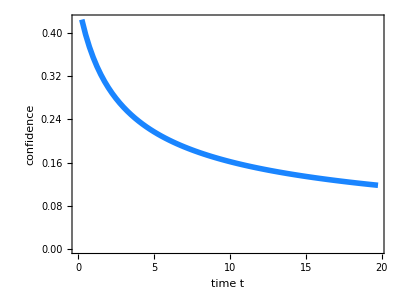

/Volumes/GoogleDrive/My Drive/DiODe/Manuscripts/DDM-on-Net/overleaf/figures/conf_acc_m02s075n1tOp.pdf

```mathematica
saveImg=True;
colours={RGBColor["#1A85FF"],RGBColor["#D41159"]}; (* Colour-blind-friendly colours *)
axesThickness=0.003;
lineThickness=0.01;
labelSize=25;
tickSize=20;
plt=ListLinePlot[Select[confData,#[[1]]==0.75&][[All,{2,3}]],
PlotRange->{Automatic,Automatic},
PlotStyle->{colours[[1]],Thickness[lineThickness]},
AspectRatio->3/4,
Joined->True,
Frame->True,
(*FrameStyle->{{{colours[[1]],Thickness[axesThickness]},Automatic},{{Gray,Thickness[axesThickness]},{Gray,Thickness[axesThickness]}}},*)
FrameStyle->Directive[{Gray,Thickness[axesThickness]}],
LabelStyle->{labelSize-2,Bold},
FrameTicksStyle->tickSize-3,
FrameLabel->{{Style["confidence",Black],""},{Style["time t",Black],""}},
ImageSize->400
]
If[saveImg,Export["/Volumes/GoogleDrive/My Drive/DiODe/Manuscripts/DDM-on-Net/overleaf/figures/conf_acc_m02s075n1tOp.pdf",plt]]
```

### Plots for Figure 2 and Figures SF1 - SF2

#### Loading data for Fig.2 and SF1

```mathematica
resDir="/Users/joefresna/DecisionsOnNetworks/results/synch_6/";
nodes=50;
netType="rgg-fixed-degree";netPar="5";
accMeanValues={0.5,0.6};
accRangeValues=Range[0.05,0.25,0.05];
colours=ColorData[97,"ColorList"];
Do[
tmpList={{},{},{},{},{},{}};
Do[
data=Import[resDir<>"out_net-"<>netType<>"_nodes-"<>ToString[nodes]<>"_link-"<>netPar<>"_model-conf-perfect_up-"<>upType<>"_accmean-"<>ToString[accMeanValues[[i]]]<>"_accrange-"<>ToString[accRange]<>".txt","Table"];
(* List of mean cost *)
AppendTo[tmpList[[1+(i-1)*3]],{accRange,Mean[data[[2;;All,5]]/nodes]}];
stdError=1.96*StandardDeviation[data[[2;;All,5]]/nodes]/Sqrt[Length[data]-1];
AppendTo[tmpList[[2+(i-1)*3]],{accRange,Mean[data[[2;;All,5]]/nodes]-stdError}];
AppendTo[tmpList[[3+(i-1)*3]],{accRange,Mean[data[[2;;All,5]]/nodes]+stdError}];
,{accRange,accRangeValues},{i,Length[accMeanValues]}];
If[upType=="optim-up",dataKick=tmpList,If[upType=="no-up",dataBase=tmpList,dataBelief=tmpList]];
,{upType,{"optim-up","no-up","belief-up"}}]
ratio={Join[Transpose[{accRangeValues}],Transpose[{dataBelief[[1,All,2]]/dataKick[[1,All,2]]}],2],
Join[Transpose[{accRangeValues}],Transpose[{dataBelief[[4,All,2]]/dataKick[[4,All,2]]}],2]
};

ratioPerRun={{},{},{},{},{},{}};
Do[
Do[
data=Import[resDir<>"out_net-"<>netType<>"_nodes-"<>ToString[nodes]<>"_link-"<>netPar<>"_model-conf-perfect_up-"<>upType<>"_accmean-"<>ToString[accMeanValues[[i]]]<>"_accrange-"<>ToString[accRange]<>".txt","Table"];
If[upType=="optim-up",dataK=data,dataB=data];
,{upType,{"optim-up","belief-up"}}];
(*Print[Show[ListPlot[dataB⟦2;;All,-1⟧],ListPlot[dataK⟦2;;All,-1⟧,PlotStyle->Red]]];*)
AppendTo[ratioPerRun[[1+(i-1)*3]],{accRange,Mean[dataK⟦2;;All,5⟧/dataB⟦2;;All,5⟧]}];
If[accRangeValues==0.05,Print[dataB⟦2;;All,5⟧]];
stdError=1.96*StandardDeviation[dataB⟦2;;All,5⟧/dataK⟦2;;All,5⟧]/Sqrt[Length[dataB]-1];
AppendTo[ratioPerRun[[2+(i-1)*3]],{accRange,Mean[dataB⟦2;;All,5⟧/dataK⟦2;;All,5⟧]-stdError}];
AppendTo[ratioPerRun[[3+(i-1)*3]],{accRange,Mean[dataB⟦2;;All,5⟧/dataK⟦2;;All,5⟧]+stdError}];
,{accRange,accRangeValues},{i,Length[accMeanValues]}];

accMeanValue=0.5;
netParValues={0,5,10,15};
dataConn={{},{},{},{},{},{},{},{},{},{},{},{}};
Do[
data=Import[resDir<>"out_net-"<>netType<>"_nodes-"<>ToString[nodes]<>"_link-"<>If[netParValues⟦i⟧==0,"5",ToString[netParValues⟦i⟧]]<>"_model-conf-perfect_up-"<>If[netParValues⟦i⟧==0,"no-up","optim-up"]<>"_accmean-"<>ToString[accMeanValue]<>"_accrange-"<>ToString[accRange]<>".txt","Table"];
(* List of mean cost *)
AppendTo[dataConn[[1+(i-1)*3]],{accRange,Mean[data[[2;;All,5]]/nodes]}];
stdError=1.96*StandardDeviation[data[[2;;All,5]]/nodes]/Sqrt[Length[data]-1];
AppendTo[dataConn[[2+(i-1)*3]],{accRange,Mean[data[[2;;All,5]]/nodes]-stdError}];
AppendTo[dataConn[[3+(i-1)*3]],{accRange,Mean[data[[2;;All,5]]/nodes]+stdError}];
,{accRange,accRangeValues},{i,Length[netParValues]}];

accMeanValue=0.5;
groupSizeValues={25,50,100};
Do[
tmpList={{},{},{},{},{},{},{},{},{}};
Do[
data=Import[resDir<>"out_net-"<>netType<>"_nodes-"<>ToString[groupSizeValues⟦i⟧]<>"_link-"<>ToString[netPar]<>"_model-conf-perfect_up-"<>upType<>"_accmean-"<>ToString[accMeanValue]<>"_accrange-"<>ToString[accRange]<>".txt","Table"];
(* List of mean cost *)
AppendTo[tmpList[[1+(i-1)*3]],{accRange,Mean[data[[2;;All,5]]/groupSizeValues⟦i⟧]}];
stdError=1.96*StandardDeviation[data[[2;;All,5]]/groupSizeValues⟦i⟧]/Sqrt[Length[data]-1];
AppendTo[tmpList[[2+(i-1)*3]],{accRange,Mean[data[[2;;All,5]]/groupSizeValues⟦i⟧]-stdError}];
AppendTo[tmpList[[3+(i-1)*3]],{accRange,Mean[data[[2;;All,5]]/groupSizeValues⟦i⟧]+stdError}];
,{accRange,accRangeValues},{i,Length[groupSizeValues]}];
If[upType=="optim-up",dataSizeO=tmpList,dataSizeB=tmpList];
,{upType,{"optim-up","belief-up"}}]

accMeanValue=0.5;
groupSizeValues={25,50,100};
Do[
tmpList={{},{},{},{},{},{},{},{},{}};
tmpList2={{},{},{}};
Do[
data=Import[resDir<>"out_net-"<>netType<>"_nodes-"<>ToString[groupSizeValues⟦i⟧]<>"_link-"<>ToString[netPar]<>"_model-conf-perfect_up-"<>upType<>"_accmean-"<>ToString[accMeanValue]<>"_accrange-"<>ToString[accRange]<>".txt","Table"];
(* List of mean cost *)
AppendTo[tmpList[[1+(i-1)*3]],{accRange,Mean[(data⟦2;;All,5⟧-data⟦2;;All,13⟧)/groupSizeValues⟦i⟧]}];
AppendTo[tmpList2[[i]],{accRange,Mean[data⟦2;;All,13⟧/groupSizeValues⟦i⟧]}];
stdError=1.96*StandardDeviation[(data⟦2;;All,5⟧-data⟦2;;All,13⟧)/groupSizeValues⟦i⟧]/Sqrt[Length[data]-1];
AppendTo[tmpList[[2+(i-1)*3]],{accRange,Mean[(data⟦2;;All,5⟧-data⟦2;;All,13⟧)/groupSizeValues⟦i⟧]-stdError}];
AppendTo[tmpList[[3+(i-1)*3]],{accRange,Mean[(data⟦2;;All,5⟧-data⟦2;;All,13⟧)/groupSizeValues⟦i⟧]+stdError}];
,{accRange,accRangeValues},{i,Length[groupSizeValues]}];
If[upType=="optim-up",posCasSizeO=tmpList,posCasSizeB=tmpList];
posInitSize=tmpList2;
,{upType,{"optim-up","belief-up"}}]

nodes=100;
netType="rgg-fixed-degree";netPar="5";
accMeanValues={0.5,0.6};
Do[
tmpList={{},{},{},{},{},{}};
tmpList2={{},{}};
Do[
data=Import[resDir<>"out_net-"<>netType<>"_nodes-"<>ToString[nodes]<>"_link-"<>netPar<>"_model-conf-perfect_up-"<>upType<>"_accmean-"<>ToString[accMeanValues[[i]]]<>"_accrange-"<>ToString[accRange]<>".txt","Table"];
(* List of mean cost *)
AppendTo[tmpList[[1+(i-1)*3]],{accRange,Mean[(data⟦2;;All,5⟧-data⟦2;;All,13⟧)/nodes]}];
AppendTo[tmpList2[[i]],{accRange,Mean[data⟦2;;All,13⟧/nodes]}];
stdError=1.96*StandardDeviation[(data⟦2;;All,5⟧-data⟦2;;All,13⟧)/nodes]/Sqrt[Length[data]-1];
AppendTo[tmpList[[2+(i-1)*3]],{accRange,Mean[(data⟦2;;All,5⟧-data⟦2;;All,13⟧)/nodes]-stdError}];
AppendTo[tmpList[[3+(i-1)*3]],{accRange,Mean[(data⟦2;;All,5⟧-data⟦2;;All,13⟧)/nodes]+stdError}];
,{accRange,accRangeValues},{i,Length[accMeanValues]}];
If[upType=="optim-up",posCasAccO=tmpList,posCasAccB=tmpList];
posInitAcc=tmpList2;
,{upType,{"optim-up","no-up","belief-up"}}]
ratio={Join[Transpose[{accRangeValues}],Transpose[{dataBelief[[1,All,2]]/dataKick[[1,All,2]]}],2],
Join[Transpose[{accRangeValues}],Transpose[{dataBelief[[4,All,2]]/dataKick[[4,All,2]]}],2]
};

nodes=50;
quorum=1;
netType="rgg-fixed-degree";netPar="5";
accRangeValues=Range[0.05,0.25,0.05];
Do[
tmpList={{},{},{}};
Do[
data=Import[resDir<>"out_net-"<>netType<>"_nodes-"<>ToString[nodes]<>"_link-"<>netPar<>"_model-conf-perfect_up-"<>upType<>"_accmean-"<>ToString[accMeanValues[[i]]]<>"_accrange-"<>ToString[accRange]<>".txt","Table"];
(* List of mean cost *)
succ=Length[Select[data⟦2;;All,5⟧,#≥nodes*quorum&]]/Length[data⟦2;;All,5⟧];
time=Mean[Select[data⟦2;;All,{4,5,6}⟧,#⟦2⟧≥nodes*quorum||#⟦3⟧≥nodes*quorum&]⟦All,1⟧];
AppendTo[tmpList[[1+(i-1)*3]],{time,succ,accRange}];
stdError=1.96*Sqrt[(1-succ)*succ/(Length[data]-1)];
AppendTo[tmpList[[2+(i-1)*3]],{time,succ-stdError,accRange}];
AppendTo[tmpList[[3+(i-1)*3]],{time,succ+stdError,accRange}];
,{accRange,Reverse[accRangeValues]},{i,1}];
If[upType=="optim-up",satoWBS=tmpList,satoBC=tmpList];
,{upType,{"optim-up","belief-up"}}]
```

#### Figure 2

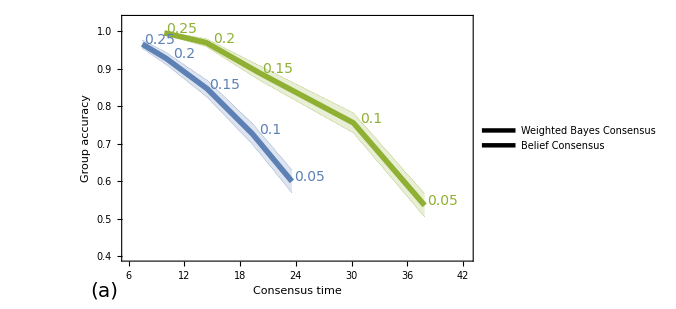

/Users/joefresna/Google Drive/DiODe/Manuscripts/DDM-on-Net/overleaf/figures/synch_n50_RGG_sato.pdf

```mathematica
saveImg=True;
frame[legend_]:=Framed[legend,FrameStyle->Gray,RoundingRadius->2,FrameMargins->0,Background->White];
lineThickness=0.008;
legendThickness=lineThickness*20;
labelSize=20;
tickSize=15;
legendSize=15;
ϵ=1.5;
imageSize=500;
numberShift={1.9,0.011};
numberFontSize=14;
plt=Show[ListPlot[Join[satoWBS⟦All,All,{1,2}⟧,satoBC⟦All,All,{1,2}⟧],
Joined->True,
PlotStyle->Flatten[Table[Join[
{Directive[{colours[[c]],Thickness[lineThickness]}]},
ConstantArray[Directive[{colours[[c]],Thickness[lineThickness/10],Dashing[0]}],2]],{c,{1,3}}]],
Filling->{1->{2},1->{3},4->{5},4->{6}},
Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
PlotRange->{{Min[satoWBS⟦All,All,1⟧]-ϵ,Max[satoBC⟦All,All,1⟧]+3ϵ},{0.4,1.03}},
FrameLabel->{"Consensus time","Group accuracy"},
Epilog->{Inset[SwatchLegend[colours[[{1,3}]],{"Weighted Bayes Consensus","Belief Consensus"},LegendFunction->frame,
LegendMarkerSize->{{30,10}},LegendMarkers->Graphics[{Thickness[legendThickness],Line[{{0,0},{10,0}}]}],LabelStyle->legendSize],Scaled[{0.73,0.1}]](*0.81,0.5*)
}],
Graphics[{Text[Style[satoWBS⟦1,1,3⟧,numberFontSize,Thick,colours⟦1⟧],satoWBS⟦1,1,{1,2}⟧+numberShift]}],
Graphics[{Text[Style[satoWBS⟦1,2,3⟧,numberFontSize,Thick,colours⟦1⟧],satoWBS⟦1,2,{1,2}⟧+numberShift]}],
Graphics[{Text[Style[satoWBS⟦1,3,3⟧,numberFontSize,Thick,colours⟦1⟧],satoWBS⟦1,3,{1,2}⟧+numberShift]}],
Graphics[{Text[Style[satoWBS⟦1,4,3⟧,numberFontSize,Thick,colours⟦1⟧],satoWBS⟦1,4,{1,2}⟧+numberShift]}],
Graphics[{Text[Style[satoWBS⟦1,5,3⟧,numberFontSize,Thick,colours⟦1⟧],satoWBS⟦1,5,{1,2}⟧+numberShift]}],
Graphics[{Text[Style[satoBC⟦1,1,3⟧,numberFontSize,Thick,colours⟦3⟧],satoBC⟦1,1,{1,2}⟧+numberShift]}],
Graphics[{Text[Style[satoBC⟦1,2,3⟧,numberFontSize,Thick,colours⟦3⟧],satoBC⟦1,2,{1,2}⟧+numberShift]}],
Graphics[{Text[Style[satoBC⟦1,3,3⟧,numberFontSize,Thick,colours⟦3⟧],satoBC⟦1,3,{1,2}⟧+numberShift]}],
Graphics[{Text[Style[satoBC⟦1,4,3⟧,numberFontSize,Thick,colours⟦3⟧],satoBC⟦1,4,{1,2}⟧+numberShift]}],
Graphics[{Text[Style[satoBC⟦1,5,3⟧,numberFontSize,Thick,colours⟦3⟧],satoBC⟦1,5,{1,2}⟧+numberShift]}],
(*Do[
Graphics[{Text[Style[dataKick⟦1,i,3⟧,15,Thick],dataKick⟦1,i,{1,2}⟧+{2,0.01}]}]
,{i,Range[1,Length[accRangeValues]]}],*)
Graphics[{Text[Style["(a)",20,Thick],Scaled[{-0.05,-0.12}]]}],PlotRangeClipping->False,
ImageSize->imageSize]
If[saveImg,Export["/Users/joefresna/Google Drive/DiODe/Manuscripts/DDM-on-Net/overleaf/figures/synch_n50_RGG_sato.pdf",plt]]
```

#### Figure SF1

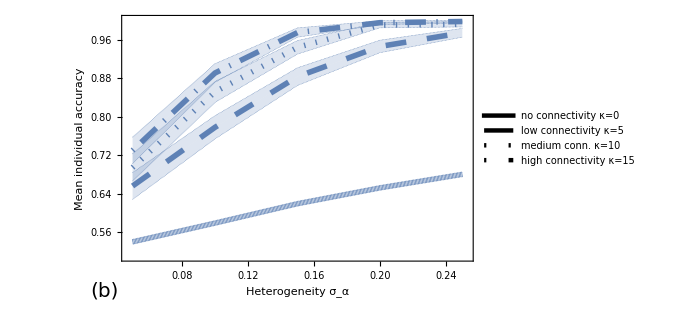

/Users/joefresna/Google Drive/DiODe/Manuscripts/DDM-on-Net/overleaf/figures/synch_n50_RGG_net.pdf

```mathematica
saveImg=True;
frame[legend_]:=Framed[legend,FrameStyle->Gray,RoundingRadius->2,FrameMargins->0,Background->White];
lineThickness=0.008;
legendThickness=lineThickness*20;
labelSize=20;
tickSize=15;
legendSize=15;
imageSize=500;
ϵ=0.0025;
plt=Show[ListPlot[dataConn,
Joined->True,
PlotStyle->Flatten[Table[Join[
{Directive[{colours[[c]],Thickness[lineThickness],Dashing[d]}]},
ConstantArray[Directive[{colours[[c]],Thickness[lineThickness/10],Dashing[0]}],2]],{c,{1,2}},{d,{0,0.03,{0.002,0.015},{0.002,0.015,0.03,0.015}}}]],
Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9},10->{11},10->{12}},
Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
PlotRange->{{Min[accRangeValues]-ϵ,Max[accRangeValues]+ϵ},Full},
FrameLabel->{"Heterogeneity σ_α","Mean individual accuracy"},
Epilog->{
Inset[SwatchLegend[ConstantArray[colours[[1]],4],{"no connectivity κ="<>ToString[netParValues⟦1⟧],"low connectivity κ="<>ToString[netParValues⟦2⟧],"medium conn. κ="<>ToString[netParValues⟦3⟧],"high connectivity κ="<>ToString[netParValues⟦4⟧]},LegendFunction->frame,
LegendMarkerSize->{{35,10}},LegendMarkers->{
Graphics[{Thickness[legendThickness],Line[{{0,0},{1,0}}]}],
Graphics[{Directive[{Thickness[legendThickness],Dashing[Large]}],Line[{{0,0},{1,0}}]}],
Graphics[{Directive[{Thickness[legendThickness],Dashing[{0.02,0.25}]}],Line[{{0,0},{1,0}}]}],
Graphics[{Directive[{Thickness[legendThickness],Dashing[{0.02,0.25,Large,0.25}]}],Line[{{0,0},{1,0}}]}]
},LabelStyle->legendSize],Scaled[{0.77,0.55}]]
}],
Graphics[{Text[Style["(b)",20,Thick],Scaled[{-0.05,-0.12}]]}],PlotRangeClipping->False,
ImageSize->imageSize]
If[saveImg,Export["/Users/joefresna/Google Drive/DiODe/Manuscripts/DDM-on-Net/overleaf/figures/synch_n50_RGG_net.pdf",plt]]
```

```mathematica
(* PLOTTING VARIABLES *)
frame[legend_]:=Framed[legend,FrameStyle->Gray,RoundingRadius->2,FrameMargins->0,Background->Null];
lineThickness=0.008;
legendThickness=lineThickness*20;
labelSize=20;
tickSize=15;
legendSize=15;
imageSize=500;
```

#### Loading data for SF2(a-b)

```mathematica
(*resDir="/Users/joefresna/DecisionsOnNetworks/results/kick_fixed_6_coste100/";*)
resDir="/Users/joefresna/DecisionsOnNetworks/results/kick_rgg_resample_set2/";
nodes=50;
missinfo="false";
netType="barabasi-albert";netPar="3";
netType="erdos-renyi";netPar="0.2";
netType="rgg-fixed-degree";netPar="5";
driftBaseValues={0.05,0.2};
driftRangeValues=Range[0.05,0.5,0.05];
colours=ColorData[97,"ColorList"];
(*dataBase={{},{},{}};
dataKick={{},{},{}};*)
Do[
threshs={{},{}};
tmpList={{},{},{},{},{},{}};
tmpList2={{},{},{},{},{},{}};
Do[
data=Import[resDir<>"out_net-"<>netType<>"_nodes-"<>ToString[nodes]<>"_link-"<>netPar<>"_up-"<>upType<>"_driftbase-"<>ToString[driftBaseValues[[i]]]<>"_driftrange-"<>ToString[NumberForm[driftRange,{3,2}]]<>"_miss-"<>missinfo<>".txt","Table"];
(* List of mean cost *)
AppendTo[tmpList[[1+(i-1)*3]],{driftRange,Mean[data[[2;;All,-1]]/nodes]}];
stdError=1.96*StandardDeviation[data[[2;;All,-1]]/nodes]/Sqrt[Length[data]-1];
AppendTo[tmpList[[2+(i-1)*3]],{driftRange,Mean[data[[2;;All,-1]]/nodes]-stdError}];
AppendTo[tmpList[[3+(i-1)*3]],{driftRange,Mean[data[[2;;All,-1]]/nodes]+stdError}];
(* List of mean accuracy *)
AppendTo[tmpList2[[1+(i-1)*3]],{driftRange,Mean[data[[2;;All,5]]/nodes]}];
stdError=1.96*StandardDeviation[data[[2;;All,5]]/nodes]/Sqrt[Length[data]-1];
AppendTo[tmpList2[[2+(i-1)*3]],{driftRange,Mean[data[[2;;All,5]]/nodes]-stdError}];
AppendTo[tmpList2[[3+(i-1)*3]],{driftRange,Mean[data[[2;;All,5]]/nodes]+stdError}];
(* List of thresholds *)
AppendTo[threshs[[i]],{driftRange,data⟦-1,-2⟧}];
,{driftRange,driftRangeValues},{i,Length[driftBaseValues]}];
If[upType=="conf-kick",dataKick=tmpList,dataBase=tmpList];
If[upType=="conf-kick",dataPosKick=tmpList2,dataPosBase=tmpList2];
,{upType,{"conf-kick","no-up"}}]
ratio={Join[Transpose[{driftRangeValues}],Transpose[{dataBase[[1,All,2]]/dataKick[[1,All,2]]}],2],
Join[Transpose[{driftRangeValues}],Transpose[{dataBase[[4,All,2]]/dataKick[[4,All,2]]}],2]
};

ratioPerRun={{},{},{},{},{},{}};
Do[
Do[
data=Import[resDir<>"out_net-"<>netType<>"_nodes-"<>ToString[nodes]<>"_link-"<>netPar<>"_up-"<>upType<>"_driftbase-"<>ToString[driftBaseValues[[i]]]<>"_driftrange-"<>ToString[NumberForm[driftRange,{3,2}]]<>"_miss-"<>missinfo<>".txt","Table"];
If[upType=="conf-kick",dataK=data,dataB=data];
,{upType,{"conf-kick","no-up"}}];
(*Print[Show[ListPlot[dataB⟦2;;All,-1⟧],ListPlot[dataK⟦2;;All,-1⟧,PlotStyle->Red]]];*)
AppendTo[ratioPerRun[[1+(i-1)*3]],{driftRange,Mean[dataB⟦2;;All,-1⟧/dataK⟦2;;All,-1⟧]}];
stdError=1.96*StandardDeviation[dataB⟦2;;All,-1⟧/dataK⟦2;;All,-1⟧]/Sqrt[Length[dataB]-1];
AppendTo[ratioPerRun[[2+(i-1)*3]],{driftRange,Mean[dataB⟦2;;All,-1⟧/dataK⟦2;;All,-1⟧]-stdError}];
AppendTo[ratioPerRun[[3+(i-1)*3]],{driftRange,Mean[dataB⟦2;;All,-1⟧/dataK⟦2;;All,-1⟧]+stdError}];
,{driftRange,driftRangeValues},{i,Length[driftBaseValues]}];
```

#### Figure SF2(a)

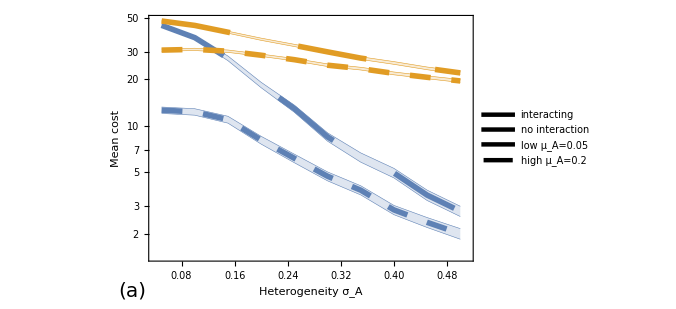

/Users/joefresna/Google Drive/DiODe/Manuscripts/DDM-on-Net/overleaf/figures/asynch_n50_RGG.pdf

```mathematica
saveImg=True;
scaling=0.19;
inset=ListPlot[Join[dataPosKick,dataPosBase],
Joined->True,
PlotStyle->Flatten[Table[Join[
{Directive[{colours[[c]],Thickness[lineThickness],Dashing[d]}]},
ConstantArray[Directive[{colours[[c]],Thickness[lineThickness/10]}],2]],{c,{1,2}},{d,{10,0.03}}]],
Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9},10->{11},10->{12}},
Frame->True,LabelStyle->labelSize*3scaling,FrameTicksStyle->tickSize*3scaling,
PlotRange->{{Min[driftRangeValues]-0.01,Max[driftRangeValues]+0.01},Full},
FrameLabel->{{None,"Mean accuracy"},{None,"Heterogeneity σ_A"}},
FrameTicks->{{None,All},{None,All}},
ImageSize->imageSize];
plt=Show[ListLogPlot[Join[dataKick,dataBase],
Joined->True,
PlotStyle->Flatten[Table[Join[
{Directive[{colours[[c]],Thickness[lineThickness],Dashing[d]}]},
ConstantArray[Directive[{colours[[c]],Thickness[lineThickness/10]}],2]],{c,{1,2}},{d,{10,0.03}}]],
Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9},10->{11},10->{12}},
Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
PlotRange->{{Min[driftRangeValues]-0.01,Max[driftRangeValues]+0.01},Full},
FrameLabel->{"Heterogeneity σ_A","Mean cost"},
Epilog->{Inset[SwatchLegend[colours[[1;;2]],{"interacting","no interaction"},LegendFunction->frame,
LegendMarkerSize->{{30,10}},LegendMarkers->Graphics[{Thickness[legendThickness],Line[{{0,0},{10,0}}]}],LabelStyle->legendSize],Scaled[{0.84,0.89}]],(*0.17,0.13 and 0.715,0.59*)
Inset[SwatchLegend[{Gray,Gray},{"low μ_A="<>ToString[driftBaseValues[[1]]],"high μ_A="<>ToString[driftBaseValues[[2]]]},LegendFunction->frame,
LegendMarkerSize->{{35,10}},LegendLabel->"Mean individual accuracy",LegendMarkers->{
Graphics[{Thickness[legendThickness],Line[{{0,0},{15,0}}]}],
Graphics[{Directive[{Thickness[legendThickness],Dashing[Large]}],Line[{{0,0},{10,0}}]}]
},LabelStyle->legendSize],Scaled[{0.79,0.57}(*Scaled[{0.21,0.14}*)]],
Inset[inset,Scaled[{0.23,0.24}],Automatic,scaling](*Scaled[{0.8,0.5}],Automatic,scaling]*)
}],
Graphics[{Text[Style["(a)",20,Thick],Scaled[{-0.05,-0.12}]]}],PlotRangeClipping->False,
ImageSize->imageSize]
If[saveImg,Export["/Users/joefresna/Google Drive/DiODe/Manuscripts/DDM-on-Net/overleaf/figures/asynch_n50_RGG.pdf",plt]]
```

#### Figure SF2(b)

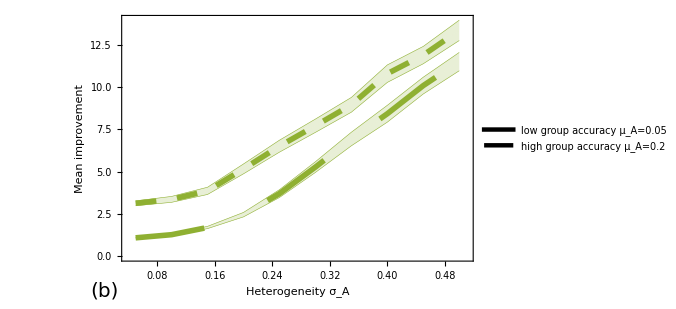

/Volumes/GoogleDrive/My Drive/DiODe/Manuscripts/DDM-on-Net/overleaf/figures/asynch_n50_RGG_impro.pdf

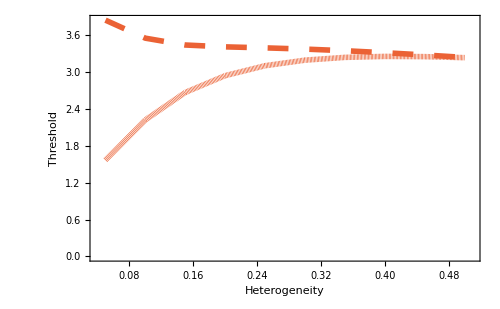
-Graphics--Graphics-

```mathematica
saveImg=True;
dashings={10,0.03};
plt=Show[ListPlot[ratioPerRun,
Joined->True,
PlotStyle->Flatten[Table[Join[
{Directive[{colours[[3]],Thickness[lineThickness],Dashing[dashings⟦c⟧]}]},
ConstantArray[Directive[{colours[[3]],Thickness[lineThickness/10]}],2]],{c,{1,2}}]],
Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9},10->{11},10->{12}},
Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
PlotRange->{{Min[driftRangeValues]-0.01,Max[driftRangeValues]+0.01},Full},
FrameLabel->{"Heterogeneity σ_A","Mean improvement"},
Epilog->{Inset[SwatchLegend[{colours⟦3⟧,colours⟦3⟧},{"low group accuracy μ_A="<>ToString[driftBaseValues[[1]]],"high group accuracy μ_A="<>ToString[driftBaseValues[[2]]]},LegendFunction->frame,
LegendMarkerSize->{{35,10}},LegendMarkers->{
Graphics[{Thickness[legendThickness],Line[{{0,0},{15,0}}]}],
Graphics[{Directive[{Thickness[legendThickness],Dashing[Large]}],Line[{{0,0},{10,0}}]}]
},LabelStyle->legendSize],Scaled[{0.71,0.12}]]
}],
Graphics[{Text[Style["(b)",20,Thick],Scaled[{-0.05,-0.12}]]}],PlotRangeClipping->False,
ImageSize->imageSize]
If[saveImg,Export["/Volumes/GoogleDrive/My Drive/DiODe/Manuscripts/DDM-on-Net/overleaf/figures/asynch_n50_RGG_impro.pdf",plt]]
plt2=ListLinePlot[threshs,
PlotStyle->Flatten[Table[{Directive[{colours[[4]],Thickness[lineThickness],Dashing[d]}]},{d,{0,0.03}}]],Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
PlotRange->{{Min[driftRangeValues]-0.01,Max[driftRangeValues]+0.01},Full},
FrameLabel->{"Heterogeneity","Threshold"},ImageSize->imageSize];
Overlay[{plt,plt2}]
```

#### Figure SF2(c)

```mathematica
resDir="/Users/joefresna/DecisionsOnNetworks/results/kick_rgg_resample_set2/";
nodes=50;
missinfo="false";
netType="rgg-fixed-degree";
netParValues={0,5,10,15};
driftBaseValue=0.05;
driftRangeValues=Range[0.05,0.5,0.05];
colours=ColorData[97,"ColorList"];
dataConn={{},{},{},{},{},{},{},{},{},{},{},{}};
Do[
data=Import[resDir<>"out_net-"<>netType<>"_nodes-"<>ToString[nodes]<>"_link-"<>If[netParValues⟦i⟧==0,"5",ToString[netParValues⟦i⟧]]<>"_up-"<>If[netParValues⟦i⟧==0,"no-up","conf-kick"]<>"_driftbase-"<>ToString[driftBaseValue]<>"_driftrange-"<>ToString[NumberForm[driftRange,{3,2}]]<>"_miss-"<>missinfo<>".txt","Table"];
(* List of mean cost *)
AppendTo[dataConn[[1+(i-1)*3]],{driftRange,Mean[data[[2;;All,-1]]/nodes]}];
stdError=1.96*StandardDeviation[data[[2;;All,-1]]/nodes]/Sqrt[Length[data]-1];
AppendTo[dataConn[[2+(i-1)*3]],{driftRange,Mean[data[[2;;All,-1]]/nodes]-stdError}];
AppendTo[dataConn[[3+(i-1)*3]],{driftRange,Mean[data[[2;;All,-1]]/nodes]+stdError}];
,{driftRange,driftRangeValues},{i,Length[netParValues]}];
```

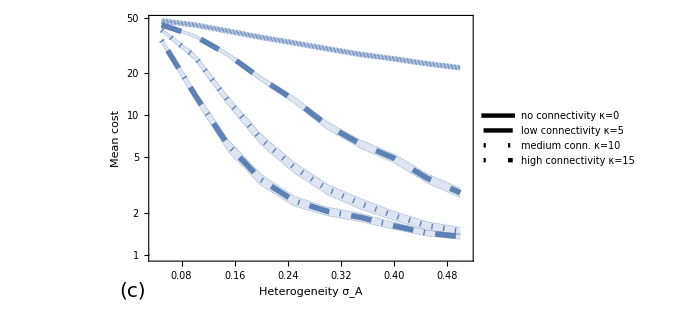

/Users/joefresna/Google Drive/DiODe/Manuscripts/DDM-on-Net/overleaf/figures/asynch_n50_RGG_net.pdf

```mathematica
saveImg=True;
frame[legend_]:=Framed[legend,FrameStyle->Gray,RoundingRadius->2,FrameMargins->0,Background->White];
lineThickness=0.008;
legendThickness=lineThickness*20;
labelSize=20;
tickSize=15;
legendSize=15;
imageSize=500;
plt=Show[ListLogPlot[dataConn,
Joined->True,
PlotStyle->Flatten[Table[Join[
{Directive[{colours[[c]],Thickness[lineThickness],Dashing[d]}]},
ConstantArray[Directive[{colours[[c]],Thickness[lineThickness/10],Dashing[0]}],2]],{c,{1,2}},{d,{0,0.03,{0.002,0.015},{0.002,0.015,0.03,0.015}}}]],
Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9},10->{11},10->{12}},
Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
PlotRange->{{Min[driftRangeValues]-0.01,Max[driftRangeValues]+0.01},Full},
FrameLabel->{"Heterogeneity σ_A","Mean cost"},
Epilog->{
Inset[SwatchLegend[ConstantArray[colours[[1]],4],{"no connectivity κ="<>ToString[netParValues⟦1⟧],"low connectivity κ="<>ToString[netParValues⟦2⟧],"medium conn. κ="<>ToString[netParValues⟦3⟧],"high connectivity κ="<>ToString[netParValues⟦4⟧]},LegendFunction->frame,
LegendMarkerSize->{{35,10}},LegendMarkers->{
Graphics[{Thickness[legendThickness],Line[{{0,0},{1,0}}]}],
Graphics[{Directive[{Thickness[legendThickness],Dashing[Large]}],Line[{{0,0},{1,0}}]}],
Graphics[{Directive[{Thickness[legendThickness],Dashing[{0.02,0.25}]}],Line[{{0,0},{1,0}}]}],
Graphics[{Directive[{Thickness[legendThickness],Dashing[{0.02,0.25,Large,0.25}]}],Line[{{0,0},{1,0}}]}]
},LabelStyle->legendSize-1],Scaled[{0.22,0.17}]]
}],
Graphics[{Text[Style["(c)",20,Thick],Scaled[{-0.05,-0.12}]]}],PlotRangeClipping->False,
ImageSize->imageSize]
If[saveImg,Export["/Users/joefresna/Google Drive/DiODe/Manuscripts/DDM-on-Net/overleaf/figures/asynch_n50_RGG_net.pdf",plt]]
```

### Plots for Figure 3

#### Figure 3 (a)

```mathematica
data005={{0.05,1e-19,0.16320063843075402},{0.05,0.030000000000000006,0.16320118419762142},{0.05,0.06000000000000001,0.16320281574672735},{0.05,0.09000000000000002,0.16320551597625454},{0.05,0.12000000000000002,0.1632092568845502},{0.05,0.15000000000000002,0.16321400029644},{0.05,0.18000000000000005,0.163219698830621},{0.05,0.21000000000000005,0.16322629706327324},{0.05,0.24000000000000005,0.16323373283616383},{0.05,0.2700000000000001,0.163241938654229},{0.05,0.30000000000000004,0.16325084311785262},{0.05,0.33000000000000007,0.16326037233842083},{0.05,0.3600000000000001,0.1632704512917075},{0.05,0.39000000000000007,0.16328100507140225},{0.05,0.4200000000000001,0.16329196001394924},{0.05,0.45000000000000007,0.16330324467497895},{0.05,0.4800000000000001,0.16331479064642804},{0.05,0.5100000000000001,0.16332653321136786},{0.05,0.5400000000000001,0.1633384118403375},{0.05,0.5700000000000001,0.1633503705383418},{0.05,0.6000000000000001,0.16336235805564667},{0.05,0.6300000000000001,0.16337432797809257},{0.05,0.6600000000000001,0.16338623871404168},{0.05,0.6900000000000002,0.1633980533954162},{0.05,0.7200000000000002,0.16340973970984107},{0.05,0.7500000000000001,0.1634212696798286},{0.05,0.7800000000000001,0.163432619403474},{0.05,0.8100000000000002,0.16344376876941935},{0.05,0.8400000000000002,0.16345470115701666},{0.05,0.8700000000000002,0.16346540313082333},{0.05,0.9000000000000001,0.16347586413683557},{0.05,0.9300000000000002,0.16348607620627276},{0.05,0.9600000000000002,0.16349603367132878},{0.05,0.9900000000000002,0.1635057328960571},{0.05,1.0200000000000002,0.16351517202452903},{0.05,1.0500000000000003,0.16352435074752933},{0.05,1.0800000000000003,0.16353327008836546},{0.05,1.1100000000000003,0.16354193220780028},{0.05,1.1400000000000001,0.16355034022770826},{0.05,1.1700000000000002,0.16355849807274275},{0.05,1.2000000000000002,0.16356641032907135},{0.05,1.2300000000000002,0.1635740821191035},{0.05,1.2600000000000002,0.16358151899104947},{0.05,1.2900000000000003,0.1635887268221073},{0.05,1.3200000000000003,0.1635957117340823},{0.05,1.3500000000000003,0.16360248002027108},{0.05,1.3800000000000003,0.1636090380824824},{0.05,1.4100000000000004,0.1636153923771416},{0.05,1.4400000000000004,0.16362154936948115},{0.05,1.4700000000000002,0.16362751549489898},{0.05,1.5000000000000002,0.1636332971266499},{0.05,1.5300000000000002,0.1636389005490923},{0.05,1.5600000000000003,0.16364433193580386},{0.1,1e-19,0.17547248428526202},{0.1,0.030000000000000006,0.17547998613389998},{0.1,0.06000000000000001,0.1755023378756854},{0.1,0.09000000000000002,0.17553908601414073},{0.1,0.12000000000000002,0.1755895003556786},{0.1,0.15000000000000002,0.17565260993996482},{0.1,0.18000000000000005,0.1757272486847035},{0.1,0.21000000000000005,0.17581210689834542},{0.1,0.24000000000000005,0.1759057846851009},{0.1,0.2700000000000001,0.1760068435911589},{0.1,0.30000000000000004,0.17611385350837933},{0.1,0.33000000000000007,0.1762254327160837},{0.1,0.3600000000000001,0.17634027985593778},{0.1,0.39000000000000007,0.17645719747763686},{0.1,0.4200000000000001,0.1765751074823005},{0.1,0.45000000000000007,0.17669305928691595},{0.1,0.4800000000000001,0.17681023183413175},{0.1,0.5100000000000001,0.17692593070017412},{0.1,0.5400000000000001,0.17703958154677923},{0.1,0.5700000000000001,0.17715072106202237},{0.1,0.6000000000000001,0.177258986378169},{0.1,0.6300000000000001,0.1773641037736685},{0.1,0.6600000000000001,0.17746587728435406},{0.1,0.6900000000000002,0.1775641776810536},{0.1,0.7200000000000002,0.17765893212556066},{0.1,0.7500000000000001,0.17775011469765842},{0.1,0.7800000000000001,0.17783773789248103},{0.1,0.8100000000000002,0.1779218451176358},{0.1,0.8400000000000002,0.17800250416987792},{0.1,0.8700000000000002,0.17807980163800058},{0.1,0.9000000000000001,0.17815383815840147},{0.1,0.9300000000000002,0.17822472443932538},{0.1,0.9600000000000002,0.1782925779663523},{0.1,0.9900000000000002,0.17835752030311236},{0.1,1.0200000000000002,0.17841967490578126},{0.1,1.0500000000000003,0.17847916537634498},{0.1,1.0800000000000003,0.1785361140869948},{0.1,1.1100000000000003,0.17859064111568726},{0.1,1.1400000000000001,0.17864286344041302},{0.1,1.1700000000000002,0.17869289434681715},{0.1,1.2000000000000002,0.17874084301032284},{0.1,1.2300000000000002,0.17878681421977627},{0.1,1.2600000000000002,0.17883090821480696},{0.1,1.2900000000000003,0.17887322061362937},{0.1,1.3200000000000003,0.17891384241193298},{0.1,1.3500000000000003,0.17895286003685232},{0.1,1.3800000000000003,0.17899035544287403},{0.1,1.4100000000000004,0.17902640623893307},{0.1,1.4400000000000004,0.17906108583798802},{0.1,1.4700000000000002,0.1790944636220438},{0.1,1.5000000000000002,0.17912660511700493},{0.1,1.5300000000000002,0.17915757217289413},{0.1,1.5600000000000003,0.17918742314594202},{0.15000000000000002,1e-19,0.19070561078994533},{0.15000000000000002,0.030000000000000006,0.19073746063225813},{0.15000000000000002,0.06000000000000001,0.1908321283799277},{0.15000000000000002,0.09000000000000002,0.1909870299481682},{0.15000000000000002,0.12000000000000002,0.1911980548713371},{0.15000000000000002,0.15000000000000002,0.19145983497564156},{0.15000000000000002,0.18000000000000005,0.19176607406964916},{0.15000000000000002,0.21000000000000005,0.19210990290920135},{0.15000000000000002,0.24000000000000005,0.19248422549982375},{0.15000000000000002,0.2700000000000001,0.19288202917376895},{0.15000000000000002,0.30000000000000004,0.19329663984331422},{0.15000000000000002,0.33000000000000007,0.19372191332658087},{0.15000000000000002,0.3600000000000001,0.19415236202568034},{0.15000000000000002,0.39000000000000007,0.19458322253436128},{0.15000000000000002,0.4200000000000001,0.1950104736554613},{0.15000000000000002,0.45000000000000007,0.1954308160159193},{0.15000000000000002,0.4800000000000001,0.19584162446567455},{0.15000000000000002,0.5100000000000001,0.1962408833140687},{0.15000000000000002,0.5400000000000001,0.19662711272440597},{0.15000000000000002,0.5700000000000001,0.19699929266788432},{0.15000000000000002,0.6000000000000001,0.19735678901014528},{0.15000000000000002,0.6300000000000001,0.197699284723683},{0.15000000000000002,0.6600000000000001,0.1980267179510091},{0.15000000000000002,0.6900000000000002,0.19833922768868265},{0.15000000000000002,0.7200000000000002,0.19863710718772912},{0.15000000000000002,0.7500000000000001,0.19892076472248285},{0.15000000000000002,0.7800000000000001,0.19919069111543303},{0.15000000000000002,0.8100000000000002,0.19944743327249595},{0.15000000000000002,0.8400000000000002,0.19969157294114429},{0.15000000000000002,0.8700000000000002,0.1999237099213601},{0.15000000000000002,0.9000000000000001,0.20014444901276296},{0.15000000000000002,0.9300000000000002,0.20035439005355407},{0.15000000000000002,0.9600000000000002,0.2005541204865631},{0.15000000000000002,0.9900000000000002,0.2007442099672279},{0.15000000000000002,1.0200000000000002,0.20092520660328567},{0.15000000000000002,1.0500000000000003,0.20109763448387777},{0.15000000000000002,1.0800000000000003,0.2012619922156637},{0.15000000000000002,1.1100000000000003,0.2014187522352401},{0.15000000000000002,1.1400000000000001,0.20156836071109305},{0.15000000000000002,1.1700000000000002,0.2017112378851396},{0.15000000000000002,1.2000000000000002,0.20184777873446125},{0.15000000000000002,1.2300000000000002,0.20197835385894777},{0.15000000000000002,1.2600000000000002,0.20210331052103545},{0.15000000000000002,1.2900000000000003,0.20222297378030452},{0.15000000000000002,1.3200000000000003,0.20233764767903334},{0.15000000000000002,1.3500000000000003,0.20244761644546103},{0.15000000000000002,1.3800000000000003,0.20255314568997917},{0.15000000000000002,1.4100000000000004,0.20265448357616006},{0.15000000000000002,1.4400000000000004,0.20275186195376785},{0.15000000000000002,1.4700000000000002,0.20284549744498717},{0.15000000000000002,1.5000000000000002,0.2029355924782503},{0.15000000000000002,1.5300000000000002,0.20302233626646504},{0.15000000000000002,1.5600000000000003,0.20310590572826187},{0.2,1e-19,0.2041732215974617},{0.2,0.030000000000000006,0.20424688400860339},{0.2,0.06000000000000001,0.20446559991844146},{0.2,0.09000000000000002,0.20482273180876112},{0.2,0.12000000000000002,0.20530778005283845},{0.2,0.15000000000000002,0.2059071445284182},{0.2,0.18000000000000005,0.20660504409253552},{0.2,0.21000000000000005,0.20738448480203733},{0.2,0.24000000000000005,0.20822817757829823},{0.2,0.2700000000000001,0.20911932973766972},{0.2,0.30000000000000004,0.21004226498813214},{0.2,0.33000000000000007,0.21098285608139009},{0.2,0.3600000000000001,0.21192877834790594},{0.2,0.39000000000000007,0.21286960850737455},{0.2,0.4200000000000001,0.21379680139475588},{0.2,0.45000000000000007,0.21470357898966508},{0.2,0.4800000000000001,0.21558476340894786},{0.2,0.5100000000000001,0.21643658030673665},{0.2,0.5400000000000001,0.21725645301592647},{0.2,0.5700000000000001,0.21804280185184208},{0.2,0.6000000000000001,0.218794857833361},{0.2,0.6300000000000001,0.21951249612432056},{0.2,0.6600000000000001,0.22019609125419912},{0.2,0.6900000000000002,0.2208463943606219},{0.2,0.7200000000000002,0.2214644311636956},{0.2,0.7500000000000001,0.2220514187338142},{0.2,0.7800000000000001,0.2226086987441318},{0.2,0.8100000000000002,0.22313768483551083},{0.2,0.8400000000000002,0.22363982182571288},{0.2,0.8700000000000002,0.22411655469464267},{0.2,0.9000000000000001,0.2245693055220064},{0.2,0.9300000000000002,0.22499945680915956},{0.2,0.9600000000000002,0.22540833986269496},{0.2,0.9900000000000002,0.22579722714208608},{0.2,1.0200000000000002,0.22616732767226394},{0.2,1.0500000000000003,0.22651978479301157},{0.2,1.0800000000000003,0.22685567566155687},{0.2,1.1100000000000003,0.22717601204496685},{0.2,1.1400000000000001,0.22748174203777005},{0.2,1.1700000000000002,0.2277737524206067},{0.2,1.2000000000000002,0.22805287144050976},{0.2,1.2300000000000002,0.228319871845243},{0.2,1.2600000000000002,0.22857547404527384},{0.2,1.2900000000000003,0.2288203493094014},{0.2,1.3200000000000003,0.2290551229254696},{0.2,1.3500000000000003,0.2292803772773461},{0.2,1.3800000000000003,0.229496654804598},{0.2,1.4100000000000004,0.22970446082295182},{0.2,1.4400000000000004,0.22990426619246887},{0.2,1.4700000000000002,0.23009650982698607},{0.2,1.5000000000000002,0.2302816010432551},{0.2,1.5300000000000002,0.2304599217517569},{0.2,1.5600000000000003,0.23063182849366431},{0.25,1e-19,0.21534216579865328},{0.25,0.030000000000000006,0.21546469793958306},{0.25,0.06000000000000001,0.2158284578895275},{0.25,0.09000000000000002,0.21642224157351034},{0.25,0.12000000000000002,0.2172283482860545},{0.25,0.15000000000000002,0.21822389265302938},{0.25,0.18000000000000005,0.21938238143732644},{0.25,0.21000000000000005,0.22067536410004515},{0.25,0.24000000000000005,0.22207398551701335},{0.25,0.2700000000000001,0.22355031283947482},{0.25,0.30000000000000004,0.22507836238650866},{0.25,0.33000000000000007,0.22663480407571843},{0.25,0.3600000000000001,0.22819936177734096},{0.25,0.39000000000000007,0.22975495453835734},{0.25,0.4200000000000001,0.23128763629942536},{0.25,0.45000000000000007,0.23278639336375256},{0.25,0.4800000000000001,0.234242853182804},{0.25,0.5100000000000001,0.23565094847794962},{0.25,0.5400000000000001,0.23700657000727746},{0.25,0.5700000000000001,0.23830723117006028},{0.25,0.6000000000000001,0.23955175905525652},{0.25,0.6300000000000001,0.24074001982632093},{0.25,0.6600000000000001,0.2418726814340582},{0.25,0.6900000000000002,0.24295101333607128},{0.25,0.7200000000000002,0.24397672083395158},{0.25,0.7500000000000001,0.24495181051202597},{0.25,0.7800000000000001,0.2458784827891392},{0.25,0.8100000000000002,0.2467590475536012},{0.25,0.8400000000000002,0.24759585908800294},{0.25,0.8700000000000002,0.24839126681287943},{0.25,0.9000000000000001,0.24914757889543426},{0.25,0.9300000000000002,0.24986703609488548},{0.25,0.9600000000000002,0.2505517937194289},{0.25,0.9900000000000002,0.251203909900258},{0.25,1.0200000000000002,0.2518253387295296},{0.25,1.0500000000000003,0.25241792708891997},{0.25,1.0800000000000003,0.25298341423187115},{0.25,1.1100000000000003,0.25352343337846567},{0.25,1.1400000000000001,0.25403951474216663},{0.25,1.1700000000000002,0.2545330895375365},{0.25,1.2000000000000002,0.25500549462237043},{0.25,1.2300000000000002,0.25545797751081567},{0.25,1.2600000000000002,0.25589170155981883},{0.25,1.2900000000000003,0.2563077511829167},{0.25,1.3200000000000003,0.256707136985692},{0.25,1.3500000000000003,0.2570908007484302},{0.25,1.3800000000000003,0.25745962020549756},{0.25,1.4100000000000004,0.2578144135892151},{0.25,1.4400000000000004,0.258155943919768},{0.25,1.4700000000000002,0.25848492303293735},{0.25,1.5000000000000002,0.25880201534489816},{0.25,1.5300000000000002,0.25910784135878034},{0.25,1.5600000000000003,0.25940298092136194},{0.3,1e-19,0.22499364883903106},{0.3,0.030000000000000006,0.22516283731441628},{0.3,0.06000000000000001,0.2256652459891658},{0.3,0.09000000000000002,0.2264858092192688},{0.3,0.12000000000000002,0.22760070689541204},{0.3,0.15000000000000002,0.22897910441795657},{0.3,0.18000000000000005,0.23058524616100912},{0.3,0.21000000000000005,0.232380650746354},{0.3,0.24000000000000005,0.23432618200780106},{0.3,0.2700000000000001,0.23638382655935414},{0.3,0.30000000000000004,0.23851807928440363},{0.3,0.33000000000000007,0.24069690545897798},{0.3,0.3600000000000001,0.24289230167965903},{0.3,0.39000000000000007,0.24508051273441545},{0.3,0.4200000000000001,0.24724197856925914},{0.3,0.45000000000000007,0.24936108823799866},{0.3,0.4800000000000001,0.2514258108878111},{0.3,0.5100000000000001,0.25342726187974496},{0.3,0.5400000000000001,0.25535924851571595},{0.3,0.5700000000000001,0.2572178268193828},{0.3,0.6000000000000001,0.25900088964145335},{0.3,0.6300000000000001,0.26070779750683704},{0.3,0.6600000000000001,0.26233905707547034},{0.3,0.6900000000000002,0.26389604756781526},{0.3,0.7200000000000002,0.26538079262022574},{0.3,0.7500000000000001,0.2667957733863721},{0.3,0.7800000000000001,0.26814377793725946},{0.3,0.8100000000000002,0.26942778183637384},{0.3,0.8400000000000002,0.2706508549770876},{0.3,0.8700000000000002,0.27181609017376185},{0.3,0.9000000000000001,0.27292654952919004},{0.3,0.9300000000000002,0.2739852251267907},{0.3,0.9600000000000002,0.274995011141033},{0.3,0.9900000000000002,0.27595868493551534},{0.3,1.0200000000000002,0.27687889515171726},{0.3,1.0500000000000003,0.27775815516680485},{0.3,1.0800000000000003,0.2785988406105034},{0.3,1.1100000000000003,0.27940318990224927},{0.3,1.1400000000000001,0.2801733069827734},{0.3,1.1700000000000002,0.2809111655965527},{0.3,1.2000000000000002,0.28161861462310794},{0.3,1.2300000000000002,0.28229738407337895},{0.3,1.2600000000000002,0.2829490914585111},{0.3,1.2900000000000003,0.283575248312024},{0.3,1.3200000000000003,0.28417726670377697},{0.3,1.3500000000000003,0.28475646562914325},{0.3,1.3800000000000003,0.285314077191526},{0.3,1.4100000000000004,0.2858512525232393},{0.3,1.4400000000000004,0.2863690674101285},{0.3,1.4700000000000002,0.28686852760071435},{0.3,1.5000000000000002,0.28735057379210033},{0.3,1.5300000000000002,0.2878160862932691},{0.3,1.5600000000000003,0.2882658893724008},{0.35000000000000003,1e-19,0.23389220858652},{0.35000000000000003,0.030000000000000006,0.23410165512266456},{0.35000000000000003,0.06000000000000001,0.23472389045309014},{0.35000000000000003,0.09000000000000002,0.23574106659002297},{0.35000000000000003,0.12000000000000002,0.23712491940137412},{0.35000000000000003,0.15000000000000002,0.2388387735578655},{0.35000000000000003,0.18000000000000005,0.2408399625796709},{0.35000000000000003,0.21000000000000005,0.24308237862786541},{0.35000000000000003,0.24000000000000005,0.24551889416799938},{0.35000000000000003,0.2700000000000001,0.24810346057052188},{0.35000000000000003,0.30000000000000004,0.2507927670460695},{0.35000000000000003,0.33000000000000007,0.25354741891197424},{0.35000000000000003,0.3600000000000001,0.256332654869141},{0.35000000000000003,0.39000000000000007,0.2591186634876964},{0.35000000000000003,0.4200000000000001,0.26188057984114044},{0.35000000000000003,0.45000000000000007,0.2645982479711973},{0.35000000000000003,0.4800000000000001,0.2672558286608776},{0.35000000000000003,0.5100000000000001,0.2698413196615605},{0.35000000000000003,0.5400000000000001,0.272346040888577},{0.35000000000000003,0.5700000000000001,0.27476412270461686},{0.35000000000000003,0.6000000000000001,0.27709202281813894},{0.35000000000000003,0.6300000000000001,0.2793280870882931},{0.35000000000000003,0.6600000000000001,0.28147216177510737},{0.35000000000000003,0.6900000000000002,0.2835252592550283},{0.35000000000000003,0.7200000000000002,0.28548927555192016},{0.35000000000000003,0.7500000000000001,0.28736675580205207},{0.35000000000000003,0.7800000000000001,0.2891607025968826},{0.35000000000000003,0.8100000000000002,0.29087442170796585},{0.35000000000000003,0.8400000000000002,0.29251139974188833},{0.35000000000000003,0.8700000000000002,0.29407520861029196},{0.35000000000000003,0.9000000000000001,0.29556943219575543},{0.35000000000000003,0.9300000000000002,0.2969976111564481},{0.35000000000000003,0.9600000000000002,0.29836320238142433},{0.35000000000000003,0.9900000000000002,0.29966955014809726},{0.35000000000000003,1.0200000000000002,0.30091986652419317},{0.35000000000000003,1.0500000000000003,0.30211721898967075},{0.35000000000000003,1.0800000000000003,0.3032645236280646},{0.35000000000000003,1.1100000000000003,0.30436454255407125},{0.35000000000000003,1.1400000000000001,0.3054198845098237},{0.35000000000000003,1.1700000000000002,0.3064330077821104},{0.35000000000000003,1.2000000000000002,0.3074062247729639},{0.35000000000000003,1.2300000000000002,0.3083417077024829},{0.35000000000000003,1.2600000000000002,0.3092414950408943},{0.35000000000000003,1.2900000000000003,0.31010749836152285},{0.35000000000000003,1.3200000000000003,0.3109415093816951},{0.35000000000000003,1.3500000000000003,0.31174520701819997},{0.35000000000000003,1.3800000000000003,0.3125201643307708},{0.35000000000000003,1.4100000000000004,0.31326785526360645},{0.35000000000000003,1.4400000000000004,0.3139896611232656},{0.35000000000000003,1.4700000000000002,0.3146868767530177},{0.35000000000000003,1.5000000000000002,0.3153607163802828},{0.35000000000000003,1.5300000000000002,0.31601231912622696},{0.35000000000000003,1.5600000000000003,0.31664275417579235},{0.4,1e-19,0.2425223386573848},{0.4,0.030000000000000006,0.24276493096186366},{0.4,0.06000000000000001,0.24348599088485076},{0.4,0.09000000000000002,0.24466586110241423},{0.4,0.12000000000000002,0.24627335546391538},{0.4,0.15000000000000002,0.24826789597771123},{0.4,0.18000000000000005,0.2506021023396143},{0.4,0.21000000000000005,0.25322453570386194},{0.4,0.24000000000000005,0.2560823250916757},{0.4,0.2700000000000001,0.25912346834624844},{0.4,0.30000000000000004,0.2622986795909235},{0.4,0.33000000000000007,0.2655627332900857},{0.4,0.3600000000000001,0.2688753186372671},{0.4,0.39000000000000007,0.27220146155821284},{0.4,0.4200000000000001,0.27551159506488526},{0.4,0.45000000000000007,0.27878136569235284},{0.4,0.4800000000000001,0.28199125911421535},{0.4,0.5100000000000001,0.28512611661519105},{0.4,0.5400000000000001,0.2881745997791102},{0.4,0.5700000000000001,0.2911286462320173},{0.4,0.6000000000000001,0.29398294619361315},{0.4,0.6300000000000001,0.2967344587131392},{0.4,0.6600000000000001,0.2993819779899088},{0.4,0.6900000000000002,0.3019257539527366},{0.4,0.7200000000000002,0.304367166966567},{0.4,0.7500000000000001,0.3067084537643984},{0.4,0.7800000000000001,0.3089524800954256},{0.4,0.8100000000000002,0.3111025548113497},{0.4,0.8400000000000002,0.3131622799176753},{0.4,0.8700000000000002,0.3151354312915111},{0.4,0.9000000000000001,0.3170258651613142},{0.4,0.9300000000000002,0.3188374459506381},{0.4,0.9600000000000002,0.3205739916351097},{0.4,0.9900000000000002,0.32223923330317966},{0.4,1.0200000000000002,0.3238367861192162},{0.4,1.0500000000000003,0.325370129346726},{0.4,1.0800000000000003,0.326842593494924},{0.4,1.1100000000000003,0.3282573530018371},{0.4,1.1400000000000001,0.32961742316517},{0.4,1.1700000000000002,0.33092566028254905},{0.4,1.2000000000000002,0.3321847641709812},{0.4,1.2300000000000002,0.33339728240696564},{0.4,1.2600000000000002,0.33456561576902577},{0.4,1.2900000000000003,0.335692024478375},{0.4,1.3200000000000003,0.336778634925359},{0.4,1.3500000000000003,0.33782744664303765},{0.4,1.3800000000000003,0.3388403393480233},{0.4,1.4100000000000004,0.3398190799152418},{0.4,1.4400000000000004,0.34076532918993396},{0.4,1.4700000000000002,0.34168064856886615},{0.4,1.5000000000000002,0.34256650630495816},{0.4,1.5300000000000002,0.34342428350664694},{0.4,1.5600000000000003,0.3442552798163331},{0.45,1e-19,0.25114482853319975},{0.45,0.030000000000000006,0.2514142075242069},{0.45,0.06000000000000001,0.2522152678514094},{0.45,0.09000000000000002,0.2535272807553512},{0.45,0.12000000000000002,0.25531730020953014},{0.45,0.15000000000000002,0.2575423408655458},{0.45,0.18000000000000005,0.26015202792117365},{0.45,0.21000000000000005,0.26309142104429567},{0.45,0.24000000000000005,0.2663037389133965},{0.45,0.2700000000000001,0.2697327719461504},{0.45,0.30000000000000004,0.27332484887765623},{0.45,0.33000000000000007,0.2770302999476087},{0.45,0.3600000000000001,0.28080442331191163},{0.45,0.39000000000000007,0.28460800596653235},{0.45,0.4200000000000001,0.2884074757564189},{0.45,0.45000000000000007,0.29217477002292547},{0.45,0.4800000000000001,0.295887003701254},{0.45,0.5100000000000001,0.299526009783882},{0.45,0.5400000000000001,0.3030778117958954},{0.45,0.5700000000000001,0.30653207399559407},{0.45,0.6000000000000001,0.3098815621122409},{0.45,0.6300000000000001,0.3131216364374705},{0.45,0.6600000000000001,0.31624979029929534},{0.45,0.6900000000000002,0.3192652403018327},{0.45,0.7200000000000002,0.3221685699572081},{0.45,0.7500000000000001,0.32496142513060555},{0.45,0.7800000000000001,0.3276462577236912},{0.45,0.8100000000000002,0.3302261129256595},{0.45,0.8400000000000002,0.3327044549031956},{0.45,0.8700000000000002,0.3350850257748249},{0.45,0.9000000000000001,0.33737173296236544},{0.45,0.9300000000000002,0.3395685604175782},{0.45,0.9600000000000002,0.3416794997043901},{0.45,0.9900000000000002,0.34370849741125953},{0.45,1.0200000000000002,0.34565941594043814},{0.45,1.0500000000000003,0.34753600489599545},{0.45,1.0800000000000003,0.34934188127052873},{0.45,1.1100000000000003,0.35108051628866094},{0.45,1.1400000000000001,0.35275522764614453},{0.45,1.1700000000000002,0.35436917586963196},{0.45,1.2000000000000002,0.3559253638318717},{0.45,1.2300000000000002,0.357426638635742},{0.45,1.2600000000000002,0.35887569523888135},{0.45,1.2900000000000003,0.36027508132082964},{0.45,1.3200000000000003,0.3616272029995219},{0.45,1.3500000000000003,0.36293433109136475},{0.45,1.3800000000000003,0.36419860767802253},{0.45,1.4100000000000004,0.36542205279926226},{0.45,1.4400000000000004,0.3666065711357233},{0.45,1.4700000000000002,0.3677539585812013},{0.45,1.5000000000000002,0.3688659086318089},{0.45,1.5300000000000002,0.369944018541495},{0.45,1.5600000000000003,0.3709897952104404},{0.5,1e-19,0.2598861303007882},{0.5,0.030000000000000006,0.2601770660423185},{0.5,0.06000000000000001,0.2610426149552097},{0.5,0.09000000000000002,0.26246149753594333},{0.5,0.12000000000000002,0.26439983328114103},{0.5,0.15000000000000002,0.2668133019606902},{0.5,0.18000000000000005,0.26964978375435267},{0.5,0.21000000000000005,0.2728521887012623},{0.5,0.24000000000000005,0.2763612073863483},{0.5,0.2700000000000001,0.2801177717632423},{0.5,0.30000000000000004,0.28406508907702493},{0.5,0.33000000000000007,0.288150186031677},{0.5,0.3600000000000001,0.29232496267386215},{0.5,0.39000000000000007,0.29654680010876877},{0.5,0.4200000000000001,0.3007787924795325},{0.5,0.45000000000000007,0.3049896842896244},{0.5,0.4800000000000001,0.30915359325788466},{0.5,0.5100000000000001,0.3132495907108258},{0.5,0.5400000000000001,0.3172611996216694},{0.5,0.5700000000000001,0.32117585743803656},{0.5,0.6000000000000001,0.3249843785057131},{0.5,0.6300000000000001,0.32868044013338854},{0.5,0.6600000000000001,0.33226010753560614},{0.5,0.6900000000000002,0.3357214060603715},{0.5,0.7200000000000002,0.33906394407024715},{0.5,0.7500000000000001,0.342288586322292},{0.5,0.7800000000000001,0.34539717537998676},{0.5,0.8100000000000002,0.348392297203874},{0.5,0.8400000000000002,0.3512770863594637},{0.5,0.8700000000000002,0.3540550660487462},{0.5,0.9000000000000001,0.35673001825535644},{0.5,0.9300000000000002,0.359305879577062},{0.5,0.9600000000000002,0.3617866587105139},{0.5,0.9900000000000002,0.36417637199767744},{0.5,1.0200000000000002,0.36647899389408845},{0.5,1.0500000000000003,0.3686984196555605},{0.5,1.0800000000000003,0.3708384379425406},{0.5,1.1100000000000003,0.3729027114048235},{0.5,1.1400000000000001,0.374894763630057},{0.5,1.1700000000000002,0.3768179711177756},{0.5,1.2000000000000002,0.37867555917939055},{0.5,1.2300000000000002,0.38047060086685713},{0.5,1.2600000000000002,0.38220601820270544},{0.5,1.2900000000000003,0.38388458512581863},{0.5,1.3200000000000003,0.3855089316846317},{0.5,1.3500000000000003,0.38708154910592113},{0.5,1.3800000000000003,0.38860479544629317},{0.5,1.4100000000000004,0.3900809015976899},{0.5,1.4400000000000004,0.39151197747021194},{0.5,1.4700000000000002,0.39290001821739134},{0.5,1.5000000000000002,0.39424691040256027},{0.5,1.5300000000000002,0.39555443803164403},{0.5,1.5600000000000003,0.39682428839882594}};
```

```mathematica
dataThresh005={{0.05,1.5684617004889438},{0.1,2.2235971811724093},{0.15000000000000002,2.671063018975889},{0.2,2.9449432564682487},{0.25,3.1064676699388576},{0.3,3.197048277341129},{0.35000000000000003,3.242294502368813},{0.4,3.258063136334146},{0.45,3.2543782180078247},{0.5,3.2377301537593324}};
```

```mathematica
data02={{0.05,0.00000000000000000010,0.08596173183378794},{0.05,0.03000000000000000583,0.08600070086035806},{0.05,0.06000000000000001166,0.0861154730664696},{0.05,0.09000000000000002442,0.08622875281452436},{0.05,0.12000000000000002331,0.10046636406464746},{0.05,0.15000000000000002220,0.10058339941062654},{0.05,0.18000000000000004885,0.10071402481356177},{0.05,0.21000000000000004774,0.10085321017822929},{0.05,0.24000000000000004663,0.10099648562590312},{0.05,0.27000000000000007327,0.10114013497177964},{0.05,0.30000000000000004441,0.1012812553785975},{0.05,0.33000000000000007105,0.1014177205219813},{0.05,0.36000000000000009770,0.10154808487216606},{0.05,0.39000000000000006883,0.10167146521028571},{0.05,0.42000000000000009548,0.10178741715757927},{0.05,0.45000000000000006661,0.10189582357283719},{0.05,0.48000000000000009326,0.10199680004971712},{0.05,0.51000000000000011990,0.10209061890573609},{0.05,0.54000000000000014655,0.10217765073781475},{0.05,0.57000000000000006217,0.1022583210431697},{0.05,0.60000000000000008882,0.10233307910510187},{0.05,0.63000000000000011546,0.10240237645482157},{0.05,0.66000000000000014211,0.10246665257194225},{0.05,0.69000000000000016875,0.10252632590924578},{0.05,0.72000000000000019540,0.1025817887366903},{0.05,0.75000000000000011102,0.10263340465688268},{0.05,0.78000000000000013767,0.10268150793750468},{0.05,0.81000000000000016431,0.10272640403735653},{0.05,0.84000000000000019096,0.10276837087969909},{0.05,0.87000000000000021760,0.10280766055916779},{0.05,0.90000000000000013323,0.1028445012660947},{0.05,0.93000000000000015987,0.10287909928280056},{0.05,0.96000000000000018652,0.10291164095695694},{0.05,0.99000000000000021316,0.10294229459276395},{0.05,1.02000000000000023981,0.10297121222544171},{0.05,1.05000000000000026645,0.10299853126144119},{0.05,1.08000000000000029310,0.1030243759780832},{0.05,1.11000000000000031974,0.10304885888368288},{0.05,1.14000000000000012434,0.10307208194377292},{0.05,1.17000000000000015099,0.1030941376817259},{0.05,1.20000000000000017764,0.10311511016342417},{0.05,1.23000000000000020428,0.10313507587613924},{0.05,1.26000000000000023093,0.10315410451171927},{0.05,1.29000000000000025757,0.10317225966378203},{0.05,1.32000000000000028422,0.10318959944800335},{0.05,1.35000000000000031086,0.10320617705387732},{0.05,1.38000000000000033751,0.10322204123558096},{0.05,1.41000000000000036415,0.10323723674882611},{0.05,1.44000000000000039080,0.10325180473986893},{0.05,1.47000000000000019540,0.10326578309218398},{0.05,1.50000000000000022204,0.103279206735676},{0.05,1.53000000000000024869,0.10329210792277176},{0.05,1.56000000000000027534,0.103304516475202},{0.05,1.59000000000000030198,0.10331646000485104},{0.05,1.62000000000000032863,0.10332796411164365},{0.05,1.65000000000000035527,0.10333905256108404},{0.05,1.68000000000000038192,0.10334974744375523},{0.05,1.71000000000000040856,0.10336006931879863},{0.1,0.00000000000000000010,0.10359349982847867},{0.1,0.03000000000000000583,0.10363373301196581},{0.1,0.06000000000000001166,0.10375247962744968},{0.1,0.09000000000000002442,0.10394411646424731},{0.1,0.12000000000000002331,0.10420000514218705},{0.1,0.15000000000000002220,0.1045094292997104},{0.1,0.18000000000000004885,0.10486063503889816},{0.1,0.21000000000000004774,0.10524180553471277},{0.1,0.24000000000000004663,0.10564184857085415},{0.1,0.27000000000000007327,0.10605093877078398},{0.1,0.30000000000000004441,0.10646081326877083},{0.1,0.33000000000000007105,0.10686485828650175},{0.1,0.36000000000000009770,0.10725804212142658},{0.1,0.39000000000000006883,0.10763675154115619},{0.1,0.42000000000000009548,0.10799858005156737},{0.1,0.45000000000000006661,0.10834210393240602},{0.1,0.48000000000000009326,0.10866666939631031},{0.1,0.51000000000000011990,0.10897220384546129},{0.1,0.54000000000000014655,0.10925905663843223},{0.1,0.57000000000000006217,0.10952786985683913},{0.1,0.60000000000000008882,0.10977947673210343},{0.1,0.63000000000000011546,0.11001482404661714},{0.1,0.66000000000000014211,0.11023491443117492},{0.1,0.69000000000000016875,0.110440764640298},{0.1,0.72000000000000019540,0.11063337632901571},{0.1,0.75000000000000011102,0.11081371638348299},{0.1,0.78000000000000013767,0.110982704422567},{0.1,0.81000000000000016431,0.11114120556163617},{0.1,0.84000000000000019096,0.11129002696658652},{0.1,0.87000000000000021760,0.11142991707166651},{0.1,0.90000000000000013323,0.11156156661542538},{0.1,0.93000000000000015987,0.11168561086882435},{0.1,0.96000000000000018652,0.11180263259897029},{0.1,0.99000000000000021316,0.11191316544075061},{0.1,1.02000000000000023981,0.11201769744541089},{0.1,1.05000000000000026645,0.11211667464698333},{0.1,1.08000000000000029310,0.11221050454028601},{0.1,1.11000000000000031974,0.11229955940256085},{0.1,1.14000000000000012434,0.11238417941833495},{0.1,1.17000000000000015099,0.11246467558653098},{0.1,1.20000000000000017764,0.11254133240234164},{0.1,1.23000000000000020428,0.11261441031551796},{0.1,1.26000000000000023093,0.11268414797269187},{0.1,1.29000000000000025757,0.11275076425506031},{0.1,1.32000000000000028422,0.11281446012485857},{0.1,1.35000000000000031086,0.11287542029501516},{0.1,1.38000000000000033751,0.11293381473660977},{0.1,1.41000000000000036415,0.1129898000384297},{0.1,1.44000000000000039080,0.11304352063230644},{0.1,1.47000000000000019540,0.11309510989708449},{0.1,1.50000000000000022204,0.11314469115315146},{0.1,1.53000000000000024869,0.11319237855886462},{0.1,1.56000000000000027534,0.11323827791664506},{0.1,1.59000000000000030198,0.11328248740339945},{0.1,1.62000000000000032863,0.11332509822602237},{0.1,1.65000000000000035527,0.11336619521494476},{0.1,1.68000000000000038192,0.11340585736011982},{0.1,1.71000000000000040856,0.11344415829575456},{0.15000000000000002,0.00000000000000000010,0.10910393958692295},{0.15000000000000002,0.03000000000000000583,0.10916814961217756},{0.15000000000000002,0.06000000000000001166,0.10935809130566133},{0.15000000000000002,0.09000000000000002442,0.10966598930757823},{0.15000000000000002,0.12000000000000002331,0.11007976648137141},{0.15000000000000002,0.15000000000000002220,0.11058419746230269},{0.15000000000000002,0.18000000000000004885,0.11116222910152154},{0.15000000000000002,0.21000000000000004774,0.11179627336196223},{0.15000000000000002,0.24000000000000004663,0.1124693184939607},{0.15000000000000002,0.27000000000000007327,0.11316576849947563},{0.15000000000000002,0.30000000000000004441,0.11387198094831724},{0.15000000000000002,0.33000000000000007105,0.1145765290018621},{0.15000000000000002,0.36000000000000009770,0.11527023780064721},{0.15000000000000002,0.39000000000000006883,0.11594605987240707},{0.15000000000000002,0.42000000000000009548,0.1165988506294948},{0.15000000000000002,0.45000000000000006661,0.11722509482040634},{0.15000000000000002,0.48000000000000009326,0.11782262161265106},{0.15000000000000002,0.51000000000000011990,0.1183903332552139},{0.15000000000000002,0.54000000000000014655,0.11892796170257611},{0.15000000000000002,0.57000000000000006217,0.11943585971730399},{0.15000000000000002,0.60000000000000008882,0.1199148276514316},{0.15000000000000002,0.63000000000000011546,0.12036597386827876},{0.15000000000000002,0.66000000000000014211,0.12079060506034003},{0.15000000000000002,0.69000000000000016875,0.1211901420515843},{0.15000000000000002,0.72000000000000019540,0.12156605665186339},{0.15000000000000002,0.75000000000000011102,0.12191982547269022},{0.15000000000000002,0.78000000000000013767,0.12225289712574006},{0.15000000000000002,0.81000000000000016431,0.12256666978777794},{0.15000000000000002,0.84000000000000019096,0.12286247665891016},{0.15000000000000002,0.87000000000000021760,0.12314157732961944},{0.15000000000000002,0.90000000000000013323,0.12340515349182014},{0.15000000000000002,0.93000000000000015987,0.12365430777850521},{0.15000000000000002,0.96000000000000018652,0.12389006480049414},{0.15000000000000002,0.99000000000000021316,0.12411337367538829},{0.15000000000000002,1.02000000000000023981,0.12432511152203694},{0.15000000000000002,1.05000000000000026645,0.12452608753223407},{0.15000000000000002,1.08000000000000029310,0.12471704733774074},{0.15000000000000002,1.11000000000000031974,0.12489867747160231},{0.15000000000000002,1.14000000000000012434,0.12507160978390455},{0.15000000000000002,1.17000000000000015099,0.12523642571736326},{0.15000000000000002,1.20000000000000017764,0.1253936603820721},{0.15000000000000002,1.23000000000000020428,0.1255438063931312},{0.15000000000000002,1.26000000000000023093,0.1256873174526288},{0.15000000000000002,1.29000000000000025757,0.12582461166996595},{0.15000000000000002,1.32000000000000028422,0.1259560746231798},{0.15000000000000002,1.35000000000000031086,0.12608206216972528},{0.15000000000000002,1.38000000000000033751,0.1262029030188918},{0.15000000000000002,1.41000000000000036415,0.12631890108021301},{0.15000000000000002,1.44000000000000039080,0.1264303376033369},{0.15000000000000002,1.47000000000000019540,0.1265374731251478},{0.15000000000000002,1.50000000000000022204,0.12664054923974524},{0.15000000000000002,1.53000000000000024869,0.12673979020633386},{0.15000000000000002,1.56000000000000027534,0.12683540440931512},{0.15000000000000002,1.59000000000000030198,0.12692758568397397},{0.15000000000000002,1.62000000000000032863,0.12701651452019622},{0.15000000000000002,1.65000000000000035527,0.12710235915567605},{0.15000000000000002,1.68000000000000038192,0.12718527656911635},{0.15000000000000002,1.71000000000000040856,0.12726541338299985},{0.2,0.00000000000000000010,0.11455783719106447},{0.2,0.03000000000000000583,0.11464705458710024},{0.2,0.06000000000000001166,0.11491135966085604},{0.2,0.09000000000000002442,0.11534102820750591},{0.2,0.12000000000000002331,0.1159208550265708},{0.2,0.15000000000000002220,0.11663147819338905},{0.2,0.18000000000000004885,0.11745092485872267},{0.2,0.21000000000000004774,0.11837438567479242},{0.2,0.24000000000000004663,0.1193244983305146},{0.2,0.27000000000000007327,0.1203346516217475},{0.2,0.30000000000000004441,0.12136754918852291},{0.2,0.33000000000000007105,0.12240675209469007},{0.2,0.36000000000000009770,0.12343861910331987},{0.2,0.39000000000000006883,0.12445225138145719},{0.2,0.42000000000000009548,0.12543928922805087},{0.2,0.45000000000000006661,0.12639362194783627},{0.2,0.48000000000000009326,0.12731105875455254},{0.2,0.51000000000000011990,0.12818899699940176},{0.2,0.54000000000000014655,0.12902610995950256},{0.2,0.57000000000000006217,0.1298220676026422},{0.2,0.60000000000000008882,0.13057729604458176},{0.2,0.63000000000000011546,0.13129277649094995},{0.2,0.66000000000000014211,0.13196988138002205},{0.2,0.69000000000000016875,0.13261024382531275},{0.2,0.72000000000000019540,0.1332156556624},{0.2,0.75000000000000011102,0.1337879895392345},{0.2,0.78000000000000013767,0.1343291406018262},{0.2,0.81000000000000016431,0.1348409839322081},{0.2,0.84000000000000019096,0.1353253444111926},{0.2,0.87000000000000021760,0.13578397623635868},{0.2,0.90000000000000013323,0.1362185498146575},{0.2,0.93000000000000015987,0.13663064424582166},{0.2,0.96000000000000018652,0.1370217439044742},{0.2,0.99000000000000021316,0.13739323802911368},{0.2,1.02000000000000023981,0.13774642243031246},{0.2,1.05000000000000026645,0.1380825026530357},{0.2,1.08000000000000029310,0.13840259808845468},{0.2,1.11000000000000031974,0.13870774665846156},{0.2,1.14000000000000012434,0.13899890979548044},{0.2,1.17000000000000015099,0.13927697751676935},{0.2,1.20000000000000017764,0.13954277345092833},{0.2,1.23000000000000020428,0.13979705971866688},{0.2,1.26000000000000023093,0.14004054160315105},{0.2,1.29000000000000025757,0.14027387196996144},{0.2,1.32000000000000028422,0.1404976554148119},{0.2,1.35000000000000031086,0.14071245213028066},{0.2,1.38000000000000033751,0.14091878149207876},{0.2,1.41000000000000036415,0.14111712537179003},{0.2,1.44000000000000039080,0.14130793118727097},{0.2,1.47000000000000019540,0.14149161470457405},{0.2,1.50000000000000022204,0.14166856260675356},{0.2,1.53000000000000024869,0.14183913484558303},{0.2,1.56000000000000027534,0.14200366679228169},{0.2,1.59000000000000030198,0.1421624712030026},{0.2,1.62000000000000032863,0.14231584001422212},{0.2,1.65000000000000035527,0.14246404598237386},{0.2,1.68000000000000038192,0.14260734418118634},{0.2,1.71000000000000040856,0.1427459733692413},{0.25,0.00000000000000000010,0.11956559512689749},{0.25,0.03000000000000000583,0.11967794022736868},{0.25,0.06000000000000001166,0.12001115049249059},{0.25,0.09000000000000002442,0.12055408393481667},{0.25,0.12000000000000002331,0.12128922703114385},{0.25,0.15000000000000002220,0.12219410446910399},{0.25,0.18000000000000004885,0.12324294774529744},{0.25,0.21000000000000004774,0.12440840584709274},{0.25,0.24000000000000004663,0.12566311139983036},{0.25,0.27000000000000007327,0.12698097222031451},{0.25,0.30000000000000004441,0.12833812300995773},{0.25,0.33000000000000007105,0.12971352985048656},{0.25,0.36000000000000009770,0.13108928242577467},{0.25,0.39000000000000006883,0.13245063311694397},{0.25,0.42000000000000009548,0.1337858504604853},{0.25,0.45000000000000006661,0.13508595139785198},{0.25,0.48000000000000009326,0.1363443670371872},{0.25,0.51000000000000011990,0.13755658422344144},{0.25,0.54000000000000014655,0.13871979290554137},{0.25,0.57000000000000006217,0.13983255842246192},{0.25,0.60000000000000008882,0.14089452942701286},{0.25,0.63000000000000011546,0.14190618576942735},{0.25,0.66000000000000014211,0.14286862657689225},{0.25,0.69000000000000016875,0.14378339602598567},{0.25,0.72000000000000019540,0.1446523429367429},{0.25,0.75000000000000011102,0.14547750970022966},{0.25,0.78000000000000013767,0.14626104600154968},{0.25,0.81000000000000016431,0.1470051430706265},{0.25,0.84000000000000019096,0.14771198461559773},{0.25,0.87000000000000021760,0.14838371115345467},{0.25,0.90000000000000013323,0.14902239487318752},{0.25,0.93000000000000015987,0.14963002273895779},{0.25,0.96000000000000018652,0.1502084859157005},{0.25,0.99000000000000021316,0.15075957398517806},{0.25,1.02000000000000023981,0.1512849727313708},{0.25,1.05000000000000026645,0.15178626453597036},{0.25,1.08000000000000029310,0.15226493063498628},{0.25,1.11000000000000031974,0.1527223546589481},{0.25,1.14000000000000012434,0.15315982701585026},{0.25,1.17000000000000015099,0.15357854978415278},{0.25,1.20000000000000017764,0.15397964186806423},{0.25,1.23000000000000020428,0.1543641442335144},{0.25,1.26000000000000023093,0.1547330250942154},{0.25,1.29000000000000025757,0.15508718495662568},{0.25,1.32000000000000028422,0.15542746146221523},{0.25,1.35000000000000031086,0.15575463398800005},{0.25,1.38000000000000033751,0.15606942798299056},{0.25,1.41000000000000036415,0.1563725190300931},{0.25,1.44000000000000039080,0.15666453663493998},{0.25,1.47000000000000019540,0.15694606773868128},{0.25,1.50000000000000022204,0.15721765997746978},{0.25,1.53000000000000024869,0.15747982468741203},{0.25,1.56000000000000027534,0.1577330396768628},{0.25,1.59000000000000030198,0.1579777517781128},{0.25,1.62000000000000032863,0.15821437919386772},{0.25,1.65000000000000035527,0.15844331365339911},{0.25,1.68000000000000038192,0.1586649223928229},{0.25,1.71000000000000040856,0.15887954997334502},{0.3,0.00000000000000000010,0.12427680771049619},{0.3,0.03000000000000000583,0.12440883112709057},{0.3,0.06000000000000001166,0.12480079300315898},{0.3,0.09000000000000002442,0.1254407004024401},{0.3,0.12000000000000002331,0.126309621803578},{0.3,0.15000000000000002220,0.127383107526992},{0.3,0.18000000000000004885,0.1286328892378922},{0.3,0.21000000000000004774,0.130028649076721},{0.3,0.24000000000000004663,0.1315396733537933},{0.3,0.27000000000000007327,0.13313625585069105},{0.3,0.30000000000000004441,0.13479077558387265},{0.3,0.33000000000000007105,0.13647842954677455},{0.3,0.36000000000000009770,0.13817764373091063},{0.3,0.39000000000000006883,0.13987021279578554},{0.3,0.42000000000000009548,0.14154123009307545},{0.3,0.45000000000000006661,0.14317887137827254},{0.3,0.48000000000000009326,0.14477408777768133},{0.3,0.51000000000000011990,0.14632025376371802},{0.3,0.54000000000000014655,0.1478128043648923},{0.3,0.57000000000000006217,0.14924888527115537},{0.3,0.60000000000000008882,0.1506270308392509},{0.3,0.63000000000000011546,0.1519468777751719},{0.3,0.66000000000000014211,0.15320891762389852},{0.3,0.69000000000000016875,0.15441428761682885},{0.3,0.72000000000000019540,0.1555645973904912},{0.3,0.75000000000000011102,0.156661787947373},{0.3,0.78000000000000013767,0.1577080187400802},{0.3,0.81000000000000016431,0.15870557872728255},{0.3,0.84000000000000019096,0.1596568174772549},{0.3,0.87000000000000021760,0.16056409277045985},{0.3,0.90000000000000013323,0.16142973159101656},{0.3,0.93000000000000015987,0.16225600184488162},{0.3,0.96000000000000018652,0.16304509256811844},{0.3,0.99000000000000021316,0.16379910077452195},{0.3,1.02000000000000023981,0.16452002343068944},{0.3,1.05000000000000026645,0.1652097533371175},{0.3,1.08000000000000029310,0.1658700779384416},{0.3,1.11000000000000031974,0.16650268028881315},{0.3,1.14000000000000012434,0.16710914156465131},{0.3,1.17000000000000015099,0.167690944652002},{0.3,1.20000000000000017764,0.16824947844420157},{0.3,1.23000000000000020428,0.16878604257216512},{0.3,1.26000000000000023093,0.1693018523582097},{0.3,1.29000000000000025757,0.1697980438382777},{0.3,1.32000000000000028422,0.17027567873956412},{0.3,1.35000000000000031086,0.17073574933323943},{0.3,1.38000000000000033751,0.1711791831070929},{0.3,1.41000000000000036415,0.1716068472221097},{0.3,1.44000000000000039080,0.17201955273147565},{0.3,1.47000000000000019540,0.17241805855130937},{0.3,1.50000000000000022204,0.172803075180371},{0.3,1.53000000000000024869,0.17317526817172446},{0.3,1.56000000000000027534,0.1735352613633557},{0.3,1.59000000000000030198,0.17388363987747865},{0.3,1.62000000000000032863,0.1742209529000001},{0.3,1.65000000000000035527,0.1745477162526161},{0.3,1.68000000000000038192,0.17486441477047615},{0.3,1.71000000000000040856,0.17517150449840432},{0.35000000000000003,0.00000000000000000010,0.12886913435644923},{0.35000000000000003,0.03000000000000000583,0.12901722899918633},{0.35000000000000003,0.06000000000000001166,0.1294572713967894},{0.35000000000000003,0.09000000000000002442,0.1301768581586739},{0.35000000000000003,0.12000000000000002331,0.1311563411991802},{0.35000000000000003,0.15000000000000002220,0.132370212490116},{0.35000000000000003,0.18000000000000004885,0.13378877510393022},{0.35000000000000003,0.21000000000000004774,0.13537990382734374},{0.35000000000000003,0.24000000000000004663,0.13711071812539546},{0.35000000000000003,0.27000000000000007327,0.13894903387582877},{0.35000000000000003,0.30000000000000004441,0.14086451413332618},{0.35000000000000003,0.33000000000000007105,0.14282949081341245},{0.35000000000000003,0.36000000000000009770,0.144819470477455},{0.35000000000000003,0.39000000000000006883,0.14681336469605696},{0.35000000000000003,0.42000000000000009548,0.14879350009650602},{0.35000000000000003,0.45000000000000006661,0.15074546578859352},{0.35000000000000003,0.48000000000000009326,0.15265785244597596},{0.35000000000000003,0.51000000000000011990,0.15452192886314017},{0.35000000000000003,0.54000000000000014655,0.15633129201580917},{0.35000000000000003,0.57000000000000006217,0.15808151708777607},{0.35000000000000003,0.60000000000000008882,0.15976982532110764},{0.35000000000000003,0.63000000000000011546,0.16139478059789997},{0.35000000000000003,0.66000000000000014211,0.1629560204583959},{0.35000000000000003,0.69000000000000016875,0.16445402252262292},{0.35000000000000003,0.72000000000000019540,0.16588990782907287},{0.35000000000000003,0.75000000000000011102,0.16726527476866943},{0.35000000000000003,0.78000000000000013767,0.16858206421343508},{0.35000000000000003,0.81000000000000016431,0.16984244984852556},{0.35000000000000003,0.84000000000000019096,0.17104875081688678},{0.35000000000000003,0.87000000000000021760,0.17220336309136625},{0.35000000000000003,0.90000000000000013323,0.17330870641474533},{0.35000000000000003,0.93000000000000015987,0.17436718401609178},{0.35000000000000003,0.96000000000000018652,0.1753811526908109},{0.35000000000000003,0.99000000000000021316,0.17635290119551697},{0.35000000000000003,1.02000000000000023981,0.17728463524253485},{0.35000000000000003,1.05000000000000026645,0.1781784676754581},{0.35000000000000003,1.08000000000000029310,0.1790364126057821},{0.35000000000000003,1.11000000000000031974,0.17986038298233153},{0.35000000000000003,1.14000000000000012434,0.18065218959762777},{0.35000000000000003,1.17000000000000015099,0.18141354299387488},{0.35000000000000003,1.20000000000000017764,0.1821460557255538},{0.35000000000000003,1.23000000000000020428,0.18285124584465842},{0.35000000000000003,1.26000000000000023093,0.1835305409045979},{0.35000000000000003,1.29000000000000025757,0.18418528231852194},{0.35000000000000003,1.32000000000000028422,0.18481672990178447},{0.35000000000000003,1.35000000000000031086,0.18542606647121002},{0.35000000000000003,1.38000000000000033751,0.1860144024070171},{0.35000000000000003,1.41000000000000036415,0.18658278010957643},{0.35000000000000003,1.44000000000000039080,0.18713217830356385},{0.35000000000000003,1.47000000000000019540,0.18766351615780455},{0.35000000000000003,1.50000000000000022204,0.1881776572011426},{0.35000000000000003,1.53000000000000024869,0.18867541302377397},{0.35000000000000003,1.56000000000000027534,0.18915754676028057},{0.35000000000000003,1.59000000000000030198,0.18962477635559513},{0.35000000000000003,1.62000000000000032863,0.1900777776187168},{0.35000000000000003,1.65000000000000035527,0.1905171870714985},{0.35000000000000003,1.68000000000000038192,0.19094360460149434},{0.35000000000000003,1.71000000000000040856,0.19135759592888552},{0.4,0.00000000000000000010,0.13345943684931244},{0.4,0.03000000000000000583,0.13362045937688402},{0.4,0.06000000000000001166,0.13409925307204193},{0.4,0.09000000000000002442,0.1348833016778656},{0.4,0.12000000000000002331,0.13595272054251437},{0.4,0.15000000000000002220,0.13728158206943344},{0.4,0.18000000000000004885,0.1388395263308109},{0.4,0.21000000000000004774,0.1405934746529683},{0.4,0.24000000000000004663,0.14250927953866516},{0.4,0.27000000000000007327,0.14455318212168985},{0.4,0.30000000000000004441,0.14669299633395042},{0.4,0.33000000000000007105,0.14889898608280838},{0.4,0.36000000000000009770,0.1511444405562475},{0.4,0.39000000000000006883,0.153405979237049},{0.4,0.42000000000000009548,0.15566363489113522},{0.4,0.45000000000000006661,0.15790076535088027},{0.4,0.48000000000000009326,0.16010384535314823},{0.4,0.51000000000000011990,0.16226218344684595},{0.4,0.54000000000000014655,0.16436759807891257},{0.4,0.57000000000000006217,0.16641408262656984},{0.4,0.60000000000000008882,0.16839747771532013},{0.4,0.63000000000000011546,0.17031516430247437},{0.4,0.66000000000000014211,0.17216578513193517},{0.4,0.69000000000000016875,0.17394899816236412},{0.4,0.72000000000000019540,0.1756652630225911},{0.4,0.75000000000000011102,0.17731565878549585},{0.4,0.78000000000000013767,0.17890173118524552},{0.4,0.81000000000000016431,0.18042536667921288},{0.4,0.84000000000000019096,0.181888689162682},{0.4,0.87000000000000021760,0.18329397700464298},{0.4,0.90000000000000013323,0.18464359704177477},{0.4,0.93000000000000015987,0.18593995283399511},{0.4,0.96000000000000018652,0.18718544473495385},{0.4,0.99000000000000021316,0.18838243964701243},{0.4,1.02000000000000023981,0.18953324863538193},{0.4,1.05000000000000026645,0.1906401108593074},{0.4,1.08000000000000029310,0.1917051825304949},{0.4,1.11000000000000031974,0.192730529832649},{0.4,1.14000000000000012434,0.19371812492705262},{0.4,1.17000000000000015099,0.19466984433239795},{0.4,1.20000000000000017764,0.19558746910409222},{0.4,1.23000000000000020428,0.19647268635274942},{0.4,1.26000000000000023093,0.1973270917344577},{0.4,1.29000000000000025757,0.1981521926247332},{0.4,1.32000000000000028422,0.19894941174887462},{0.4,1.35000000000000031086,0.1997200910933838},{0.4,1.38000000000000033751,0.20046549596316204},{0.4,1.41000000000000036415,0.20118681908360503},{0.4,1.44000000000000039080,0.20188518466995248},{0.4,1.47000000000000019540,0.2025616524094089},{0.4,1.50000000000000022204,0.2032172213161605},{0.4,1.53000000000000024869,0.20385283343246186},{0.4,1.56000000000000027534,0.20446937735861132},{0.4,1.59000000000000030198,0.20506769160206634},{0.4,1.62000000000000032863,0.2056485677415793},{0.4,1.65000000000000035527,0.2062127534064246},{0.4,1.68000000000000038192,0.20676095507386674},{0.4,1.71000000000000040856,0.20729384069020235},{0.45,0.00000000000000000010,0.1381113468208378},{0.45,0.03000000000000000583,0.13828275822095748},{0.45,0.06000000000000001166,0.13879274923912166},{0.45,0.09000000000000002442,0.1396288781904359},{0.45,0.12000000000000002331,0.1407713301816541},{0.45,0.15000000000000002220,0.1421941734535195},{0.45,0.18000000000000004885,0.14386689492948745},{0.45,0.21000000000000004774,0.14575604729147248},{0.45,0.24000000000000004663,0.14782685228979608},{0.45,0.27000000000000007327,0.15004463779492117},{0.45,0.30000000000000004441,0.1523760287546062},{0.45,0.33000000000000007105,0.15478985494892084},{0.45,0.36000000000000009770,0.1572577743968383},{0.45,0.39000000000000006883,0.1597546371365375},{0.45,0.42000000000000009548,0.16225862925481885},{0.45,0.45000000000000006661,0.16475124509599665},{0.45,0.48000000000000009326,0.1672171305428907},{0.45,0.51000000000000011990,0.1696438434734596},{0.45,0.54000000000000014655,0.17202156343216915},{0.45,0.57000000000000006217,0.17434277935829737},{0.45,0.60000000000000008882,0.17660197584407272},{0.45,0.63000000000000011546,0.1787953319211276},{0.45,0.66000000000000014211,0.1809204424426803},{0.45,0.69000000000000016875,0.18297606609436667},{0.45,0.72000000000000019540,0.18496190305660531},{0.45,0.75000000000000011102,0.18687840206635373},{0.45,0.78000000000000013767,0.18872659560676844},{0.45,0.81000000000000016431,0.19050796104947254},{0.45,0.84000000000000019096,0.19222430512768834},{0.45,0.87000000000000021760,0.19387766895813466},{0.45,0.90000000000000013323,0.19547025086170106},{0.45,0.93000000000000015987,0.19700434438643816},{0.45,0.96000000000000018652,0.19848228915926586},{0.45,0.99000000000000021316,0.1999064324482707},{0.45,1.02000000000000023981,0.20127909958066048},{0.45,1.05000000000000026645,0.20260257161638967},{0.45,1.08000000000000029310,0.20387906891435398},{0.45,1.11000000000000031974,0.20511073944300726},{0.45,1.14000000000000012434,0.20629965087559107},{0.45,1.17000000000000015099,0.20744778567618521},{0.45,1.20000000000000017764,0.2085570385234769},{0.45,1.23000000000000020428,0.20962921553939728},{0.45,1.26000000000000023093,0.21066603489065416},{0.45,1.29000000000000025757,0.2116691284152271},{0.45,1.32000000000000028422,0.212640043995707},{0.45,1.35000000000000031086,0.21358024845851156},{0.45,1.38000000000000033751,0.21449113082498686},{0.45,1.41000000000000036415,0.2153740057785032},{0.45,1.44000000000000039080,0.2162301172425176},{0.45,1.47000000000000019540,0.21706064198940206},{0.45,1.50000000000000022204,0.21786669321972657},{0.45,1.53000000000000024869,0.2186493240675092},{0.45,1.56000000000000027534,0.21940953099947041},{0.45,1.59000000000000030198,0.22014825708617533},{0.45,1.62000000000000032863,0.2208663951306251},{0.45,1.65000000000000035527,0.22156479064579862},{0.45,1.68000000000000038192,0.22224424467718865},{0.45,1.71000000000000040856,0.22290551646980544},{0.5,0.00000000000000000010,0.14285495882777283},{0.5,0.03000000000000000583,0.14303477142150228},{0.5,0.06000000000000001166,0.14357003447576555},{0.5,0.09000000000000002442,0.1444484939737734},{0.5,0.12000000000000002331,0.14565059242023054},{0.5,0.15000000000000002220,0.14715065374215222},{0.5,0.18000000000000004885,0.14891833885593556},{0.5,0.21000000000000004774,0.15092021794412794},{0.5,0.24000000000000004663,0.15312131529430809},{0.5,0.27000000000000007327,0.15548651103172548},{0.5,0.30000000000000004441,0.1579817220075403},{0.5,0.33000000000000007105,0.16057482278843238},{0.5,0.36000000000000009770,0.1632363006624671},{0.5,0.39000000000000006883,0.16593966477959696},{0.5,0.42000000000000009548,0.16866163984733443},{0.5,0.45000000000000006661,0.1713821901097805},{0.5,0.48000000000000009326,0.17408441237607333},{0.5,0.51000000000000011990,0.1767543383699195},{0.5,0.54000000000000014655,0.17938067939201005},{0.5,0.57000000000000006217,0.1819545412404857},{0.5,0.60000000000000008882,0.18446912917098257},{0.5,0.63000000000000011546,0.18691945877280192},{0.5,0.66000000000000014211,0.18930208269809376},{0.5,0.69000000000000016875,0.19161483962126294},{0.5,0.72000000000000019540,0.19385662875210843},{0.5,0.75000000000000011102,0.1960272110220014},{0.5,0.78000000000000013767,0.19812703652496347},{0.5,0.81000000000000016431,0.20015709678869995},{0.5,0.84000000000000019096,0.20211879984957792},{0.5,0.87000000000000021760,0.20401386580299427},{0.5,0.90000000000000013323,0.2058442404088912},{0.5,0.93000000000000015987,0.20761202438245163},{0.5,0.96000000000000018652,0.2093194161397954},{0.5,0.99000000000000021316,0.21096866595979474},{0.5,1.02000000000000023981,0.2125620397375369},{0.5,1.05000000000000026645,0.21410179072548338},{0.5,1.08000000000000029310,0.21559013787116832},{0.5,1.11000000000000031974,0.21702924955907707},{0.5,1.14000000000000012434,0.2184212317449787},{0.5,1.17000000000000015099,0.21976811963126044},{0.5,1.20000000000000017764,0.22107187217268556},{0.5,1.23000000000000020428,0.2223343688233652},{0.5,1.26000000000000023093,0.22355740803971946},{0.5,1.29000000000000025757,0.22474270714229225},{0.5,1.32000000000000028422,0.2258919032133675},{0.5,1.35000000000000031086,0.22700655476922535},{0.5,1.38000000000000033751,0.2280881439972456},{0.5,1.41000000000000036415,0.2291380793904898},{0.5,1.44000000000000039080,0.23015769864722382},{0.5,1.47000000000000019540,0.2311482717313176},{0.5,1.50000000000000022204,0.23211100401260124},{0.5,1.53000000000000024869,0.23304703942504407},{0.5,1.56000000000000027534,0.23395746359557457},{0.5,1.59000000000000030198,0.23484330690868338},{0.5,1.62000000000000032863,0.23570554748134062},{0.5,1.65000000000000035527,0.23654511403053347},{0.5,1.68000000000000038192,0.23736288862166377},{0.5,1.71000000000000040856,0.2381597092907348}};
```

```mathematica
dataThresh02={{0.05,3.8484502803342666},{0.1,3.555214568254125},{0.15000000000000002,3.4439219014277276},{0.2,3.4136203302321335},{0.25,3.397282824234619},{0.3,3.3773727078310225},{0.35000000000000003,3.350849699829483},{0.4,3.318432803119978},{0.45,3.2815876367828403},{0.5,3.241700445355233}};
```

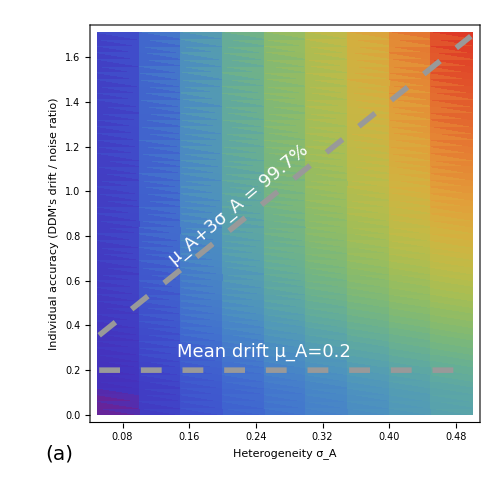

/Volumes/GoogleDrive/My Drive/DiODe/Manuscripts/DDM-on-Net/overleaf/figures/kickSize_onDrift.png

```mathematica
saveImg=True;
baseDrift=0.2;
ϵ=0.002;
frame[legend_]:=Framed[legend,FrameStyle->Gray,RoundingRadius->2,FrameMargins->0,Background->White];
lineThickness=0.008;
legendThickness=lineThickness*20;
labelSize=20;
tickSize=15;
legendSize=15;
dashing=0.03;
grayLevel=0.6;
textSize=18;
imageSize=500;
plt=Show[
ListDensityPlot[If[baseDrift==0.2,data02,data005],FrameLabel->{"Heterogeneity σ_A","Individual accuracy (DDM's drift / noise ratio)"},
LabelStyle->Directive[{labelSize,Black}],FrameTicksStyle->tickSize,
ImageSize->imageSize,PlotRangePadding->0,
ColorFunction->"Rainbow",
Mesh->None,
PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->Style["Expected impact of individual's decision",labelSize,GrayLevel[0.]],LabelStyle->{legendSize,Black}],Above]
],
Plot[{baseDrift+3*x},{x,Min[data02⟦All,1⟧]+ϵ,Max[data02⟦All,1⟧]-ϵ},PlotStyle->Directive[{Dashing[dashing],Thickness[lineThickness],GrayLevel[grayLevel]}]],
Graphics[{{Directive[{Dashing[dashing],Thickness[lineThickness],GrayLevel[grayLevel]}],Line[{{Min[data02⟦All,1⟧]+ϵ,baseDrift},{Max[data02⟦All,1⟧]-ϵ,baseDrift}}]},
{Text[Style["Mean drift μ_A="<>ToString[baseDrift],textSize,Thick,GrayLevel[2grayLevel]],{0.25,baseDrift+0.08}]},
{Text[Style[Rotate["μ_A+3σ_A = 99.7%",40Degree],textSize,Thick,GrayLevel[2grayLevel]],{0.22,0.66+baseDrift+0.08}]},
{Text[Style["(a)",20,Thick],Scaled[{-0.08,-0.08}]]}
}],PlotRangeClipping->False
]
If[saveImg,Export["/Volumes/GoogleDrive/My Drive/DiODe/Manuscripts/DDM-on-Net/overleaf/figures/kickSize_onDrift.png",plt]]
```

#### Figure 3 (c)

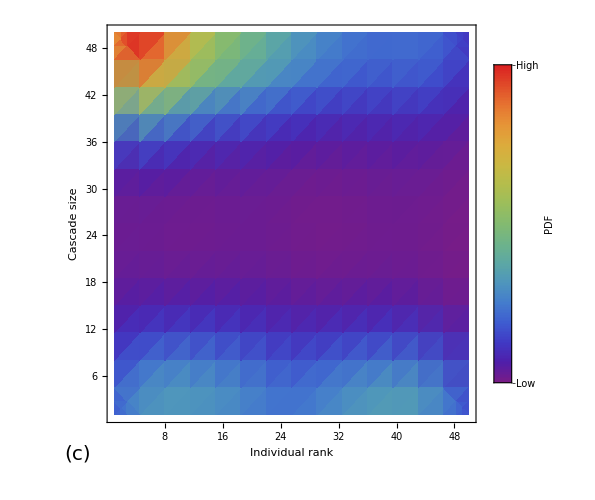

/Volumes/GoogleDrive/My Drive/DiODe/Manuscripts/DDM-on-Net/overleaf/figures/emergent_leaders_s50_k10_d005_h05.png

```mathematica
saveImg=True;
(*resDir="/Volumes/T7 Touch/Projects/DecisionsOnNetworks/results/kick_rgg_resample/";*)
resDir="/Users/joefresna/DecisionsOnNetworks/results/kick_rgg_resample_set2/";
nodes=50;
missinfo="false";
netType="rgg-fixed-degree";netPar="10";
driftBaseValue=0.05;
driftRangeValue=0.5;
upTypeFix="conf-kick";
colorScheme=ColorData[{"Rainbow",{0,70}}];
labelSize=20;
tickSize=15;
imageSize=500;

tmpList={{},{},{},{},{},{}};
dataCas=Import[resDir<>"out_net-"<>netType<>"_nodes-"<>ToString[nodes]<>"_link-"<>netPar<>"_up-"<>upTypeFix<>"_driftbase-"<>ToString[driftBaseValue]<>"_driftrange-"<>ToString[NumberForm[driftRangeValue,{3,2}]]<>"_miss-"<>missinfo<>"_cas.txt","Table"];
plt=Show[
SmoothDensityHistogram[dataCas⟦2;;All,{1,2}⟧,Automatic,"PDF",
FrameLabel->{"Individual rank","Cascade size"},
FrameStyle->Directive[{labelSize,Black}],
(*ScalingFunctions->"Log",*)
FrameTicksStyle->tickSize,
PlotRangePadding->0,
ColorFunction->"Rainbow",
(*PlotLabel->"Emergent Leaders",*)
PlotLegends->BarLegend[{"Rainbow",{0,1}},LegendLayout->"Column","Ticks"->{0,1},"TickLabels"->{"Low","High"},LegendLabel->"PDF",LegendMarkerSize->300],
LabelStyle->labelSize,
PlotRange->Full,
ImageSize->imageSize
],
Graphics[{Text[Style["(c)",20,Thick],Scaled[{-0.08,-0.08}]]}],
PlotRangeClipping->False]
If[saveImg,Export["/Volumes/GoogleDrive/My Drive/DiODe/Manuscripts/DDM-on-Net/overleaf/figures/emergent_leaders_s"<>ToString[nodes]<>"_k"<>ToString[netPar]<>"_d"<>StringReplace[ToString[driftBaseValue],"."->""]<>"_h05.png",plt]]
```